# What Can We Learn about Engineering and Innovation from Half a Century of the Game of Life Cellular Automaton?

## Metaengineering and Laws of Innovation

Things are invented.  Things are discovered.  And somehow there’s an arc of progress that’s formed.  But are there what amount to “laws of innovation” that govern that arc of progress?

There are some exponential and other laws that purport to at least measure overall quantitative aspects of progress (number of transistors on a chip; number of papers published in a year; etc.)  But what about all the disparate innovations that make up the arc of progress?  Do we have a systematic way to study those?

We can look at the plans for different kinds of bicycles or rockets or microprocessors.  And over the course of years we’ll see the results of successive innovations.  But most of the time those innovations won’t stay within one particular domain---say shapes of bicycle frames.  Rather they’ll keep on pulling in innovations from other domains---say, new materials or new manufacturing techniques.  But if we want to get closer to the study the pure phenomenon of innovation we need a case where--preferably over a long period of time---everything that happens can be described in a uniform way within a single narrowly defined framework.

Well, some time ago I realized that, actually, yes, there is such a case---and I’ve even personally been following it for about half a century.  It’s the effort to build “engineering” structures within the Game of Life cellular automaton. They might serve as clocks, wires, logic gates, or things that generate digits of π.  But the point is that they’re all just patterns of bits.  So when we talk about innovation in this case, we’re talking about the rather pure question of how patterns of bits get invented, or discovered.

I must say that as a long-time bystander I’ve been frustrated by how messy, specific and whimsical what the things people do with the Game of Life have often seemed to me to be.  But what I now realize is that all that detail and all that hard work have now created what amounts to a unique dataset of engineering innovation.  And my goal here is to do what one can call “metaengineering”---and to study in effect the arc of what happened in that process of engineering over the nearly six decades since the Game of Life was invented.

We’ll see in rather pure form many phenomena that are at least anecdotally familiar from our overall experience of progress and innovation.  Most of the time, the first step is to identify an objective: some purpose one can describe and wants to achieve.  (Much more rarely, one instead observes something that happens, then realizes there’s a way one can meaningfully make use of it.)  But starting from an objective, one either takes components one has, and puts human effort into arranging them to “invent” something that will achieve the objective---or in effect (usually at least somewhat systematically, and automatically) one searches to try to “discover” new ways to achieve the objective.

As we explore what’s been done with the Game of Life we’ll see occasional sudden advances---together with much larger amounts of incremental progress.  We’ll see towers of technology being built, and we’ll see old, rather simple technology being used to achieve new objectives.  But most of all, we’ll see an interplay between what gets discovered by searching possibilities---and what gets invented by explicit human effort.

The Principle of Computational Equivalence implies that there is, in a sense, infinite richness to what a computational system like the Game of Life can ultimately do.  But when it comes to engineering and technology the crucial question is what we choose to make it do---and what paths we follow get there.  Inevitably, some of this is determined by the underlying computational structure of the system.  But much of it is a reflection of how we, as humans, do things, and the patterns of choices we make.  And that’s what we’ll be able to study---at quite large scale---by looking at the nearly six decades of work on the Game of Life.

But how similar are the results of such “purposeful engineering” to the results of “blind” adaptive evolution of the kind that occurs in biology?  I recently explored adaptive evolution (as it happens, using cellular automata as a model) and saw that it can routinely deliver what seem like “sequences of new ideas”.  But now in the example of the Game of Life we have what we explicitly identify as “sequences of new ideas”.  And so we’re in a position to compare the results of human effort (aided, in many cases, by exhaustive search) with what we can “automatically” do by the algorithmic process of adaptive evolution.

## The Nature of the Game of Life

Here’s a typical example of what it looks like to run the Game of Life:

Create animation analogous to https://conwaylife.com/wiki/R-pentomino
Cut off gliders
Make the length 1103 case; possibly minimize cuboids

PM: done below?

```mathematica
frames = 
Table[
ArrayPlot[CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}}, 0}, {{{i}}, {-25, 35}, {-45, 45}}], Mesh->True,MeshStyle->Opacity[.1]], {i, 500}];
```

```mathematica
Export["anim2.mp4", frames]
```

There’s a lot of complicated---and hard to understand---stuff going on here.  But there are still some recognizable structures---like the “blinkers” that alternate on successive steps

[[ another video ]]

PM: from Willem below

```mathematica
AnimationVideo[(ArrayPlot[ArrayPad[#,{1,1}],Mesh->True,MeshStyle->Opacity[.2],ImageSize->200]&/@CellularAutomaton["GameOfLife",{$LifeData["Blinker"]["MatrixData"],0},24])[[i]], {i, 1, 24, 1}]
```

and the “gliders” that steadily move across the screen:

[[ another video ]]

PM: from Willem below

```mathematica
AnimationVideo[(ArrayPlot[ArrayPad[#,{1,1}],Mesh->True,MeshStyle->Opacity[.2],ImageSize->200]&/@CellularAutomaton["GameOfLife",{$LifeData["Glider"]["MatrixData"],0},48])[[i]], {i, 1, 48, 1}]
```

AnimationVideo::prpchg: Warning: the output frame rate changed from 48/5 to 9598367/1000000.

Seeing these structures might make one think that one should be able to do “engineering” in the Game of Life, setting up patterns that can ultimately do all sorts of things.  And indeed our main subject here is the actual development of such engineering over the past nearly six decades since the introduction of the Game of Life.

What we’ll be concentrating on is essentially the “technology” of the Game of Life: how we take the “raw material” that the Game of Life provides, and make from it “meaningful engineering structures”.

But what about the science of the Game of Life?  What can we say about what the Game of Life “naturally does”, independent of “useful” structures we create in it?  This type of question is the subject of what I now call ruliology---a kind of science that I’ve been energetically pursuing since the early 1980s.

Within ruliology, the Game of Life is a fairly typical “class 4” 2D cellular automaton (in my numbering scheme, it’s the 2-color 9-neighbor cellular automaton with outer totalistic code 224).

I’ve always found it difficult to get a good sense of what’s going in a 2D cellular automaton by looking at a video.  With a class 4 rule like the Game of Life it often helps to have still frames that include “trails” of what’s happened before, and we’ll often use that type of visualization in what follows:

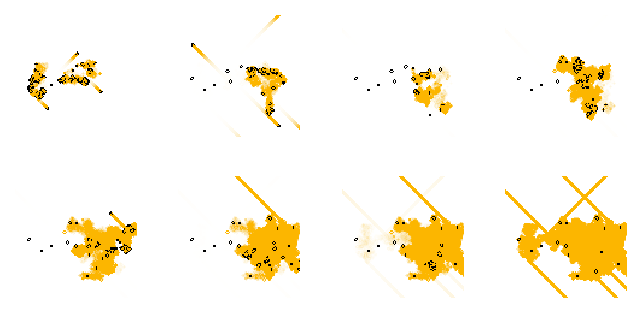

```mathematica
GraphicsGrid[Partition[CellularAutomatonHistoryPlot["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{#,{-50,50},{-50,50}},Mesh->(#<100),"Decay"-><|150->.9,300->.95,450-> .95, 600->.98,750->.985,900->.99,1050-> .995,  1200->.999|>[#]]&/@{150,300,450,600,750,900,1050,1200}, 4]]
```

To get a more global view of behavior it’s sometimes also useful to look at the whole (2+1)-dimensional “spacetime history”:

Generate 150, 300, 1200 steps.  In final case, cut off region so gliders poke through.
Label plots tucked on left underneath, in gray   (150 steps)   etc.

For Developer

```mathematica
GraphicsRow[CellularAutomatonPlot3D["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},#]&/@{150,300,1120}]
```

-Graphics-

Taking a slice through this to form “silhouettes” we get pictures that look remarkably similar to what I generated starting in the early 1980s with 1D cellular automata:

Investigate slices to take  
Or could be complete silhouettes

Label frames.  Use 150, 300, 600, 1200.  Cut off gliders at fixed width in final picture

For Developer

```mathematica
GraphicsRow[CellularAutomatonSpacetimePlot["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},#,"Decay"->.99,Mesh->(#<200)]&/@{150,300,600,900}]
```

-Graphics-

Can we try for more color variation, e.g. based on depth?

PM: from Jeremy in FromJeremy->2025-02-25-ActionItems-GoL-Design-jeremyd-v3.nb

```mathematica
GraphicsRow[CellularAutomatonSpacetimePlot["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},#,"Decay"->.99,Mesh->(#<101),ColorRules->{-1->Black, x_/; x!=-1:>Blend[RGBColor/@{Hue[0., 0., 1.],RGBColor[0.99, 0.7128, 0.],Hue[0.1, 1, 0.93]},Min[x,1] Max[(Min[#,900]/900),.5]]}]&/@{150,300,600,900}]
```

-Graphics-

Such pictures highlight the computational irreducibility that’s close at hand even in the Game of Life.  And indeed it’s the presence of such computational irreducibility that ultimately makes possible the richness of engineering that can be done in the Game of Life.  But in actually doing that engineering---and in setting up structures and processes that behave in understandable and “technologically useful” ways---we need to keep the computational irreducibility “bottled up”.  And in the end, we can think of the path of engineering innovation in the Game of Life as like an effort to navigate through an ocean of computational irreducibility, finding “islands of reducibility” that achieve the purposes we want.

## What’s Been Made in the Game of Life?

Most of the structures of “engineering interest” in the Game of Life are somehow persistent.  The simplest are structures that just remain constant, some small examples being:

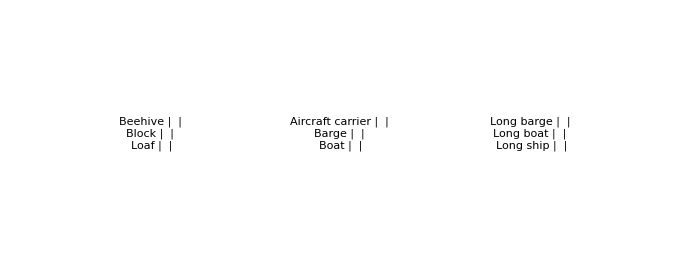

```mathematica
GraphicsRow[Grid[CellularAutomatonCompositePlot[#,{{"Trails",10,.9}->{Automatic, 60},{"3D",6}->{60, 60}}]&/@#,Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{2->1, 2.5}]&/@ Partition[{"Beehive","Block","Loaf","Aircraft carrier","Barge","Boat","Long barge","Long boat","Long ship"},3], Spacings->{38, Automatic}]
```

And, yes, structures in the Game of Life have been given all sorts of (usually whimsical) names, which I’ll use here.  (And, in that vein, structures in the Game of Life that remain constant are normally called “still lifes”.)

Beyond structures that just remain constant, there are “oscillators” that produce periodic patterns:

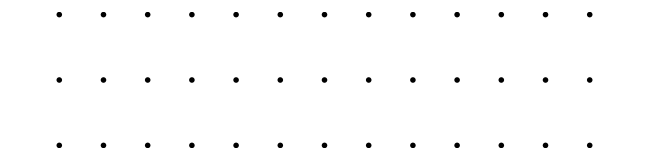

```mathematica
GraphicsGrid[ArrayPlot[ArrayPad[#,{1,1}],Mesh->True,MeshStyle->Opacity[.2],ImageSize->50]&/@CellularAutomaton["GameOfLife",{$LifeData[#]["MatrixData"],0},12]&/@{"Blinker","Traffic light","Figure eight"},Spacings->{10,20}]
```

We’ll be discussing oscillators at much greater length below, but here are a few examples (where now we’re including a visualization that shows “trails”):

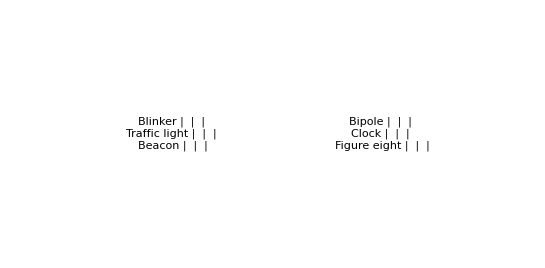

```mathematica
GraphicsRow[Grid[CellularAutomatonCompositePlot[#,{"Static"->{60, 60},{"Trails",10,.9}->{60, 60},{"3D",6}->{60, 60}}]&/@#,Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{1}, 2.5}]&/@Partition[{"Blinker","Traffic light","Beacon","Bipole","Clock","Figure eight","Figure eight"},3],Spacings->30]
```

Next in our inventory of classes of structures come “gliders” (or in general “spaceships”): structures that repeat periodically but move when they do so.  A classic example is the basic glider, which takes on the same form every 4 steps---after moving 1 cell horizontally and 1 cell vertically:

```mathematica
GraphicsGrid[ArrayPlot[ArrayPad[#,{1,1}],Mesh->True,MeshStyle->Opacity[.2],ImageSize->50]&/@CellularAutomaton["GameOfLife",{$LifeData[#]["MatrixData"],0},12]&/@{"Glider"},Spacings->{10,0}]
```

-Graphics-

Here are a few small examples of such “spaceship”-style structures:

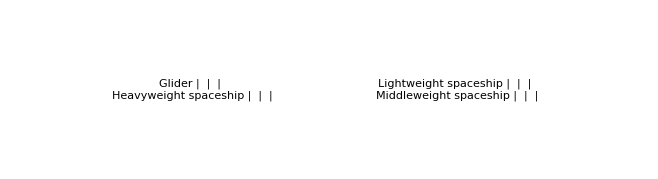

```mathematica
GraphicsRow[Grid[CellularAutomatonCompositePlot[#,{"Static"->{60, 60},{"Trails",20,.9}->{100, 60},{"3D",8}->{60, 60}},"Margin"-> 1, "Transform"-> If[# === "Glider", Identity, (Reverse/@#&)]]&/@#,Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{1}, 2.5}]&/@Partition[{"Glider","Heavyweight spaceship","Lightweight spaceship","Middleweight spaceship"},2],Spacings->30]
```

Still lifes, oscillators and spaceships are most of what one sees in the “ash” that survives from typical random initial conditions.  And for example the end result (after 1103 steps) from the evolution we saw in the previous section consists of:

Fix cell sizes
Line up etc.
Should say 8×   etc.
Align by numbers at the top

For Developer

```mathematica
GraphicsGrid[With[{ca=PatternElements[CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{{{1104}}}]]},{KeyValueMap[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#,0},8,ImageSize->50],Text[StringJoin[ToString[#2],"×"]],Top]&,ca],KeyValueMap[CellularAutomatonPlot3D["GameOfLife",{#,0},14,ImageSize->{Automatic,100}]&,ca]}]]
```

-Graphics-

The structures we’ve seen so far were all found quickly after the Game of Life was invented; indeed, pretty much as soon it was simulated on a computer.  But one feature that they all share is that they don’t systematically grow; they always return to the same number of black cells.  And so one of the early surprises (in 1970) was the discovery of a “glider gun” that shoots out a glider every 30 steps forever:

Have this loop at correct number of frames

Noted for Arianag/Markl

```mathematica
AnimationVideo[ArrayPlot[CellularAutomaton["GameOfLife",{$LifeData["Gosper glider gun"]["MatrixData"], 0}, {{{i}}, {-5, 35}, {-5, 45}}], Mesh->True,MeshStyle->Opacity[.05],ImageSize->250], {i, 1, 200, 1}]
```

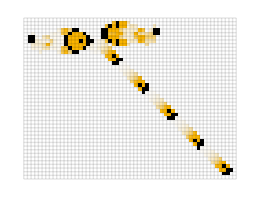
-Graphics--Graphics3D--Graphics-

```mathematica
Row[{CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Gosper glider gun"]["MatrixData"], 0},150,ImageSize->260],CellularAutomatonPlot3D["GameOfLife",{$LifeData["Gosper glider gun"]["MatrixData"], 0},100,ImageSize->140,ViewPoint->{-2.198487002413733,-2.3413385931086927,1.0652645176845457}],CellularAutomatonSpacetimePlot["GameOfLife",{$LifeData["Gosper glider gun"]["MatrixData"], 0},250,"Decay"->.99,ImageSize->95,Mesh->None]},Spacer[30]]
```

Something that gives a sense of progress that’s been made in Game-of-Life “technology” is that a “more efficient” glider gun---with period 15---was discovered, but only in 2024, 54 years after the previous one:

Spacing needs to be fixed

For Developer

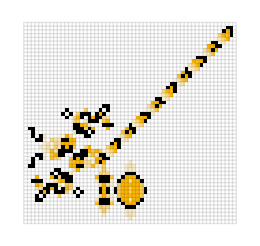
-Graphics--Graphics3D--Graphics-

```mathematica
Row[{CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Period-15 glider gun"]["MatrixData"], 0},150,ImageSize->260,"Decay"->.7],CellularAutomatonPlot3D["GameOfLife",{$LifeData["Period-15 glider gun"]["MatrixData"], 0},100,ImageSize->304,ViewPoint->{3.0373115164062576,-1.449486231706877,0.35175050305311767}],CellularAutomatonSpacetimePlot["GameOfLife",{$LifeData["Period-15 glider gun"]["MatrixData"], 0},250,"Decay"->.99,ImageSize->90,Mesh->None]},Spacer[0]]
```

Another kind of structure that was quickly discovered in the early history of the Game of Life is a “puffer”---a “spaceship” that “leaves debris behind” (in this case every 128 steps}.

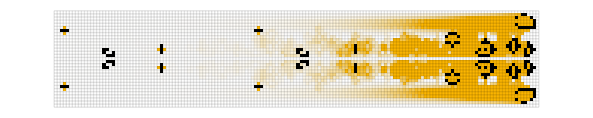

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{Reverse/@Transpose[$LifeData["Puffer 1"]["MatrixData"]], 0},300,"Decay"->.97]
```

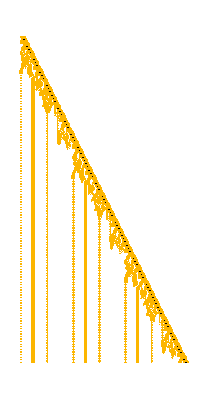

```mathematica
GraphicsRow[Join[CellularAutomatonPlot3D["GameOfLife",{$LifeData["Puffer 1"]["MatrixData"],0},#,ViewPoint->{2.8443765188744194,-1.8320647919555706,0.055324650497145265},ImageSize->{Automatic,340}]&/@{100,300},{CellularAutomatonSpacetimePlot["GameOfLife",{Reverse/@Transpose[$LifeData["Puffer 1"]["MatrixData"]], 0},400,ImageSize->{Automatic,320},"Decay"->.97,Mesh->None]}],Spacings->30]
```

But given these kinds of “components”, what can one build?  Something constructed very early was the “breeder”, that uses streams of gliders to create glider guns, that themselves then generate streams of gliders:

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Breeder 1"]["MatrixData"],0},300,Mesh->None]
```

-Graphics-

```mathematica
CellularAutomatonPlot3D["GameOfLife",{$LifeData["Breeder 1"]["MatrixData"],0},300,ViewPoint->{1.1216495614439776,-2.5887426117046104,1.8682381945719146}]
```

-Graphics-

```mathematica
CellularAutomatonSpacetimePlot["GameOfLife",{$LifeData["Breeder 1"]["MatrixData"],0},300,Mesh->None,"Decay"->.995]
```

-Graphics-

The original pattern covers about a quarter million cells (with 4060 being black).  Running it for 1000 steps we see it builds up a triangle containing a quadratically increasing number of gliders:

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Breeder 1"]["MatrixData"],0},1000,Mesh->None]
```

-Graphics-

OK, but knowing that it’s in principle possible to “fill a growing region of space”, is there a more efficient way to do it?  The surprisingly simple answer, as discovered in 1993, is yes:

```mathematica
GraphicsRow[Join[{ArrayPlot[ArrayPad[$LifeData["Spacefiller 1"]["MatrixData"],1],Mesh->True,MeshStyle->Opacity[.1]]},Map[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Spacefiller 1"]["MatrixData"],0},#,Mesh->True,MeshStyle->Opacity[.1]]&,{20,50}]],Spacings->10]
```

-Graphics-

```mathematica
GraphicsRow[CellularAutomatonPlot3D["GameOfLife",{$LifeData["Spacefiller 1"]["MatrixData"],0},#]&/@{20,50}]
```

-Graphics-

So what other kinds of things can be built in the Game of Life?  Lots---even from the simple structures we’ve seen so far.  For example, here’s a pattern that was constructed to compute the primes

```mathematica
r = Import["https://www.conwaylife.com/patterns/primer.rle"];
```

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{r,0},1600,Mesh->None,"Decay"->.97, FrameTicks->{False,Table[{60*Prime[i] - 115, Prime[i]}, {i, 1,6}]}]
```

-Graphics-

emitting a “lightweight spaceship” at step 100+120n only if n is prime.  It’s a little more obvious how this works when it’s viewed “in spacetime”; in effect it’s running a sieve in which all multiples of all numbers are instantiated as streams of gliders, which knock out spaceships generated at non-prime positions:

```mathematica
Show[CellularAutomatonSpacetimePlot["GameOfLife",{Import["https://www.conwaylife.com/patterns/primer.rle"],0},1600,Mesh->None,"Decay"->.99],FrameTicks->{Table[{60*Prime[i] - 115, Prime[i]}, {i, 1,5}], False, False, False}]
```

-Graphics-

If we look at the original pattern here, it’s just made up of a collection of rather simple structures:

Fix x’s
Align images at the top

For Developer

```mathematica
Style[Row[KeyValueMap[Labeled[ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.2],ImageSize->30],Text[Style[StringTemplate["``×"][#2]]],Top]&,ReverseSort@PatternElements[Import["https://www.conwaylife.com/patterns/primer.rle"]]]," "],LineSpacing->{1,1}]
```

-Graphics-89×-Graphics-79×-Graphics-24×-Graphics-21×-Graphics-19×-Graphics-12×-Graphics-11×-Graphics-9×-Graphics-8×-Graphics-6×-Graphics-6×-Graphics-5×-Graphics-5×-Graphics-5×-Graphics-5×-Graphics-5×-Graphics-4×-Graphics-4×-Graphics-4×-Graphics-4×-Graphics-3×-Graphics-3×-Graphics-3×-Graphics-3×-Graphics-3×-Graphics-3×-Graphics-2×-Graphics-2×-Graphics-2×-Graphics-2×-Graphics-2×-Graphics-2×-Graphics-2×-Graphics-2×-Graphics-2×-Graphics-1×-Graphics-1×-Graphics-1×-Graphics-1×-Graphics-1×-Graphics-1×

And indeed structures like these have been used to build all sorts of things, including for example Turing machine emulators---and also an emulator for the Game of Life itself, with this 499×499 pattern corresponding to a single emulated Life cell:

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["p5760 unit Life cell"]["MatrixData"],0},200,Mesh->None,"Decay"->.95]
```

-Graphics-

Both these last two patterns were constructed in the 1990s---from components that had been known since the early 1970s.  And---as we can see---they’re large (and complicated).   But do they need to be so large?  One of the lessons of the Principle of Computational Equivalence is that in the computational universe there’s almost always a way to “do just as much, but with much less”.  And indeed in the Game of Life many, many discoveries along these lines have been made in the past few decades.

As we’ll see, often (but not always) these discoveries built on “new devices” and “new mechanisms” that were identified in the intervening years.  A long series of such “devices” and “mechanisms” involved handling “signals” associated with streams of gliders.  For example, the “glider pusher” (from 1993) has the somewhat subtle (but useful) effect of “pushing” a glider by one cell when it goes past:

```mathematica
GraphicsRow[{GraphicsGrid[Partition[Table[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Glider pusher"]["MatrixData"],0},{4 n,{-2,25},{-2,28}},"Decay"->.93],{n,2,9}],4], ImageSize-> {Automatic, 200}],CellularAutomatonPlot3D["GameOfLife",{$LifeData["Glider pusher"]["MatrixData"],0},40,ViewPoint->{2.088321875639556,-2.6284768080224388,0.42428930391120906},ImageSize->{Automatic,200}, PlotRangePadding->None]}]
```

-Graphics-

Another example (actually already known in 1971, and based on the period-15 “pentadecathlon” oscillator) is a glider reflector:

Probably add light mesh  (or change lighting)

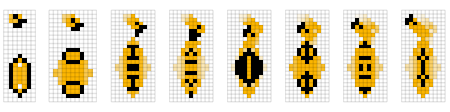
-Graphics--Graphics3D-

```mathematica
Row[{GraphicsRow[Table[CellularAutomatonHistoryPlot["GameOfLife",{Transpose@{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0}},0},t,"Decay"->.9],{t,2,32,4}],ImageSize->450],CellularAutomatonPlot3D["GameOfLife",{Transpose@{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,1,1,1,0,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0}},0},32,ViewPoint->{3.354257140174464,-0.4332240339889044,0.10618838902163552},ImageSize->110]},Spacer[20]]
```

PM: from Jeremy: second example. Jeremy prefers this example. EdgeForm[GrayLevel[0, .15]] + different view angle + custom lighting

This one is good.  But the code needs to be cleaned

For Developer

```mathematica
Show[ReplaceRepeated[-Graphics3D-,EdgeForm[None]->EdgeForm[GrayLevel[0,.15]]],
Lighting->,ViewPoint->{3.146,-1.095,0.593},ViewVertical->{-0.412,0.066,0.908},ImageSize->115]
```

-Graphics3D-

But a feature of both this glider pusher and glider reflector is that they work only when both the glider and the stationary object are in a particular phase with respect to their periods.  And this makes it very tricky to build larger structures out of these that operate correctly (and in many cases it wouldn’t be possible but for the commensurability of the period 30 of the original glider gun, and the period 15 of the glider reflector).

Could glider pushing and glider reflection be done more robustly?  The answer turns out to be yes.  Though it wasn’t until 2020 that the “bandersnatch” was created---a completely static structure that “pushes” gliders independent of their phase:

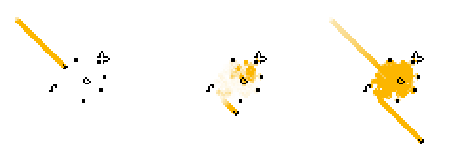
-Graphics--Graphics3D-

```mathematica
Row[{GraphicsRow[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Bandersnatch"]["MatrixData"],0},{#,{0,70},{0,60}},Mesh->None,"Decay"->#2]&@@@{{100,.99},{200,.9},{260,.99}},ImageSize->460],CellularAutomatonPlot3D["GameOfLife",{$LifeData["Bandersnatch"]["MatrixData"],0},{{80,220}},ImageSize->{102,Automatic}]},Spacer[20]]
```

Meanwhile, in 2013 the “snark” had been created---which served as a phase-independent glider reflector:

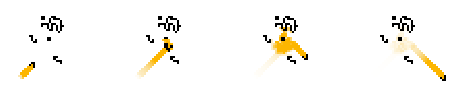
-Graphics--Graphics3D-

```mathematica
Row[{GraphicsRow[CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},{#,{0,35},{0,40}},Mesh->None,"Decay"->#2]&@@@{{20,.95},{60,.95},{100,.95},{140,.95}},ImageSize->460],CellularAutomatonPlot3D["GameOfLife",{$LifeData["Snark"]["MatrixData"],0},90,Mesh->True,MeshStyle->Opacity[.1],ViewPoint->{-3.1109281250378347,-0.02451443444705201,1.330986567682907},ImageSize->72]},Spacer[20]]
```

One theme---to which we’ll return later---is that after certain functionality was first built in the Game of Life, there followed many “optimizations”, achieving that functionality more robustly, with smaller patterns, etc.  An important methodology has revolved around so-called “hasslers”, which in effect allow one to “mine” small pieces of computational irreducibility, by providing “harnesses” that “rein in” behavior, typically returning patterns to their original states after it’s done what one wants it to do.

So, for example, here’s a hassler (found, as it happens just on February 8, 2025!) that “harnesses” the first pattern we looked at above (that didn’t stabilize for 1103 steps) into an oscillator with period 80:

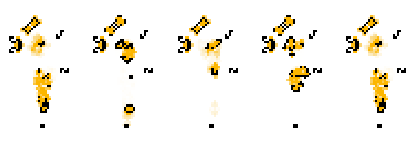
-Graphics--Graphics3D-

```mathematica
Row[{GraphicsRow[Table[CellularAutomatonHistoryPlot["GameOfLife",{Transpose[SparseArray[…]],0},t,Mesh->None],{t,80,160,20}],ImageSize->415],CellularAutomatonPlot3D["GameOfLife",{SparseArray[…],0},{{30,160+30}},ImageSize->115]},Spacer[20]]
```

And based on this (indeed, later that same day) the most-compact-ever “spaceship gun” was constructed from this:

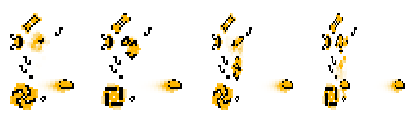
-Graphics--Graphics3D-

```mathematica
Row[{GraphicsRow[Table[CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},t,Mesh->None],{t,78,150,20}],ImageSize->415],CellularAutomatonPlot3D["GameOfLife",{SparseArray[…],0},{{78,160+30}},ImageSize->220]},Spacer[5]]
```

## The Arc of Progress

We’ve talked about some of what it’s been possible to build in the Game of Life over the years.  Now I want to talk about how that happened, or, in other words, the “arc of progress” in the Game of Life.  And as a first indication of this, we can plot the number of new Life structures that have been identified each year (or, more specifically, the number of structures deemed significant enough to name, and to record in the LifeWiki database or its predecessors):

Sketch of history: GoL-17

Note to self

Use the blue color here, non-hackily

For Developer

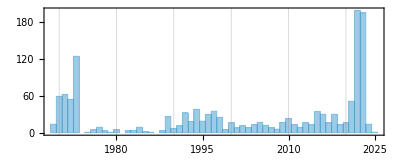

```mathematica
Histogram[{{},Values[#Year&/@$LifeData]},{1},Frame->True,AspectRatio->.4,FrameLabel->{"year",None},GridLines->{Range[1970,2020,10],None}]
```

There’s an immediate impression of several waves of activity.  And we can break this down into plots for various common categories of structures:

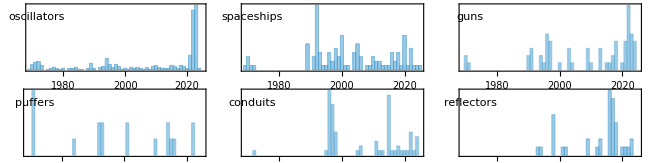

```mathematica
GraphicsGrid[Partition[KeyValueMap[Histogram[{{},#2},{1},PlotRange->{{1969,2025},Automatic},Frame->True,FrameTicks->{Automatic,None},AspectRatio->.3,ImageSize->200,PlotRangePadding->{Automatic,{0,Scaled[.15]}},Epilog->Style[Text[ToLowerCase[Pluralize@#1],Scaled[{.06,.8}],{-1,0}],11]]&,],3],ImageSize->650,Spacings->{3,7}]
```

For oscillators we see fairly continuous activity for five decades, but with rapid acceleration recently.  For “spaceships” and “guns” we see a long dry spell from the early 1970s to the 1990s, followed by fairly consistent activity since.  And for conduits and reflectors we see almost nothing until sudden peaks of activity, in the mid-1990s and mid-2010s respectively.

But what was actually done to find all these structures?  There have basically been two methods: construction and search.  Construction is a story of “explicit engineering”---and of using human thought to build up what one wants. Search, on the other hand, is a story of automation---and of taking algorithmically generated (usually large) collections of possible patterns, and testing them to find what one wants.  Particularly in more recent times it’s also become common to interleave these methods, for example using construction to build a framework, and then using search to find specific patterns that implement some feature of that framework.

When one uses construction, it’s like “inventing” a structure, and when one uses search, it’s like “discovering” it.  So how much of each is being done in practice?  Text mining descriptions of recently recorded structures the result is as follows---indicating that, at least in recent times, search (i.e. “discovery”) has become the dominant methodology for finding new structures:

Cut off 2025

```mathematica
fdata=Import["https://conwaylife.com/wiki/LifeWiki:News_archive","FullData"];
```

```mathematica
ydata=Discard[fdata[[4,5,7,1,5;;-1]],Flatten[#]==={}&];
```

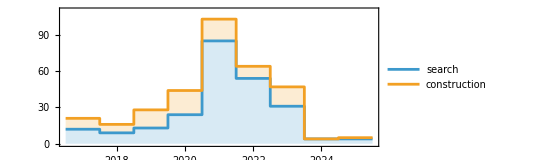

```mathematica
ListStepPlot[Reverse/@Transpose[Most[{Total@Sign@StringCount[#,"discover"|"use"],Total@Sign@StringCount[#,"construct"]}&/@ydata]],Center,PlotLayout->"Stacked",Filling->{2->{1},1->Axis},Frame->True,PlotRange->{{0.5,Automatic},{0,110}},PlotLegends->{"search","construction"},AspectRatio->.4,FrameTicks->{{Automatic,None},{Transpose[{Range[2,8],Riffle[Range[2018,2025,2],None]}],Automatic}}]
```

PM: from Willem below

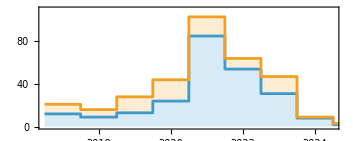

```mathematica
ListStepPlot[Reverse/@Transpose[Most[{Total@Sign@StringCount[#,"discover"|"use"],Total@Sign@StringCount[#,"construct"]}&/@ydata]],Center,PlotLayout->"Stacked",Filling->{2->{1},1->Axis},Frame->True,PlotRange->{{0.5,8.5},{0,110}},PlotLegends->{"search","construction"},AspectRatio->.4,FrameTicks->{{Automatic,None},{Transpose[{Range[2,8],Riffle[Range[2018,2024,2],None]}],Automatic}}]
```

ArrayPlot[{{0,1,1},{1,1,0},{0,1,0}},Frame->None,ImageSize->15]

Noted for Arianag/Markl

When the Game of Life was being invented, it wasn’t long before it was being run on computers---and people were trying to classify the things it could do.  Still lifes and simple oscillators showed up immediately.  And then---evolving from the  (“R pentomino”) initial condition that we used at the beginning here---after 69 steps something unexpected showed up.  In between complicated behavior that was hard to describe was a simple free-standing structure that just systematically moved---a “glider”:

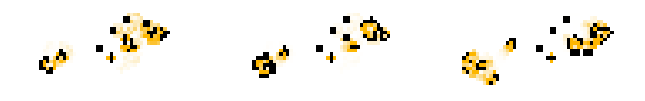

```mathematica
GraphicsRow[CellularAutomatonHistoryPlot["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{#,{-10,10},{-30,17}},Mesh->False,"Decay"->.7]&/@{70,74,83}]
```

Some other moving structures (dubbed “spaceships”) were also observed.  But the question arose: could there be a structure that would somehow systematically grow forever?  To find it involved a mixture of “discovery” and “invention”.  In running from the  (“R pentomino”) initial condition lots of things happen.  But at step 785 it was noticed that there appeared the following structure:

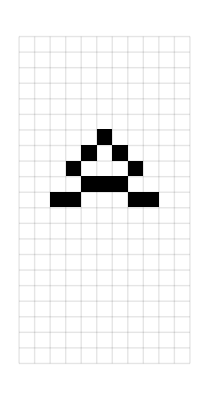
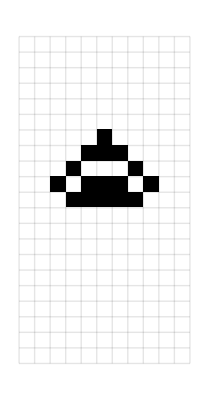
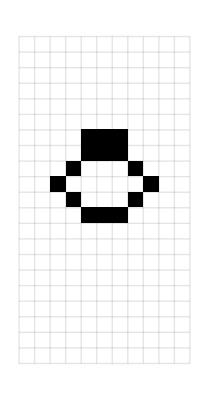
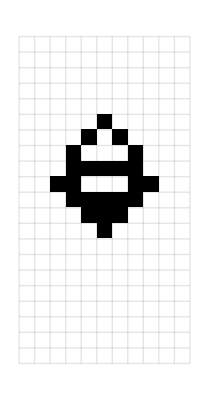
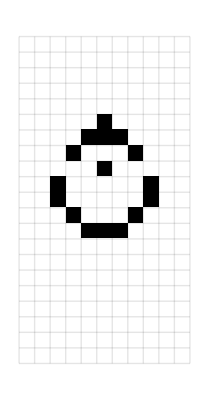
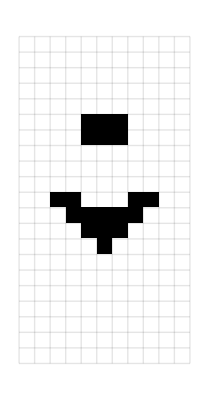
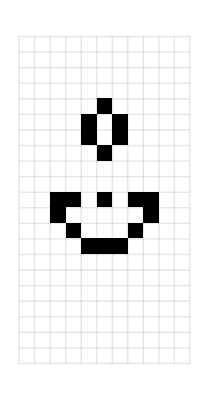
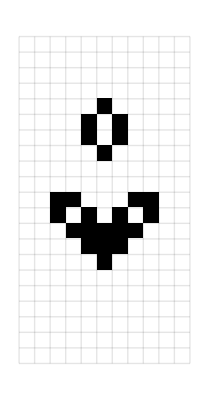

```mathematica
GraphicsGrid[Partition[ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife",{$LifeData["Queen bee"]["MatrixData"],0},36],18]]
```

For a while this structure (dubbed the “queen bee”) behaves in a fairly orderly way---producing two stable “beehive” structures (visible here as vertical columns).  But then it “decays” into more complicated behavior:

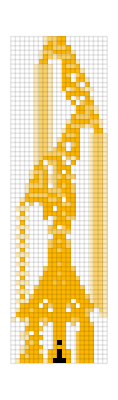

```mathematica
GraphicsRow[{CellularAutomatonPlot3D["GameOfLife",{$LifeData["Queen bee"]["MatrixData"],0},70,ViewPoint->{3.1309623028268923,0.5424157801164059,1.1631251780258365}],CellularAutomatonSpacetimePlot["GameOfLife",{Transpose@$LifeData["Queen bee"]["MatrixData"],0},70,"Decay"->.9]}]
```

But could this “discovered” behavior be “stabilized”?  The answer was that, yes, if a “queen bee” was combined with two “blocks” it would just repeatedly “shuttle” back and forth:

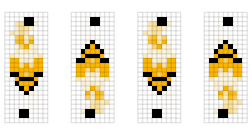

```mathematica
GraphicsRow[CellularAutomatonHistoryPlot["GameOfLife",{Transpose@$LifeData["Queen bee shuttle"]["MatrixData"], 0},#,ImageSize->260]&/@Range[45,90,15],Spacings->40]
```

What about two “queen bees”?  Now whenever these collided there was a side effect: a glider was generated---with the result that the whole structure became a glider gun repeatedly producing gliders forever:

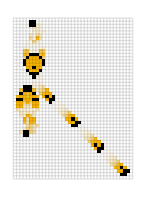

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{Transpose@$LifeData["Gosper glider gun"]["MatrixData"], 0},120,ImageSize->260]
```

The glider gun was the first major example of a structure in the Game of Life that was found---at least in part---by construction.  And within a year of it being found in November 1970, two more guns---with very similar methods of operation---had been found:

PM: from Jeremy, “Stephen specs looks good...   Opacity[.1] for typical cases... and Opacity[.05] for ‘high density’ cases”, nb in FromJeremy->2025-02-25-ActionItems-GoL-Design-jeremyd-v3.nb

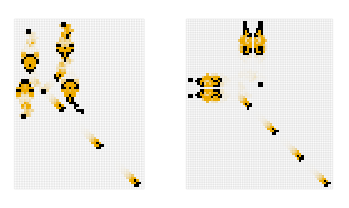

```mathematica
GraphicsRow[CellularAutomatonHistoryPlot["GameOfLife",{Transpose@$LifeData[#]["MatrixData"], 0},150,MeshStyle->Opacity[.05],ImageSize->{Automatic,250}]&/@{"Period-60 glider gun","New gun 1"}]
```

But then the well ran dry---and no further gun was found until 1990.  Pretty much the same thing happened with spaceships: four were found in 1970, but no more were found until 1989.  As we’ll discuss later, it was in a sense a quintessential story of computational irreducibility: there was no way to predict (or “construct”) what spaceships would exist; one just had to do the computation (i.e. search) to find out.

It was, however, easier to have incremental success with oscillators---and (as we’ll see) pretty much every year an oscillator with some new period was found, essentially always by search.  Some periods were “long holdouts” (for example the first period-19 oscillator was found only in 2023), once again reflecting the effects of computational irreducibility.

Glider guns provided a source of “signals” for Life engineering.  But what could one do with these signals?  An important idea---that first showed up in the “breeder” in 1971---was “glider synthesis”: the concept that combinations of gliders could produce other structures.  So, for example, it was found that three carefully-arranged gliders could generate a period-15 (“pentadecathlon”) oscillator:

```mathematica
GraphicsRow[ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife",{SparseArray[…],0},13]]
```

-Graphics-

It was also soon found that 8 gliders could make the original glider gun (the breeder made glider guns by a slightly more ornate method).  And eventually there developed the conjecture that any structure that could be synthesized from gliders would need at most 15 gliders, carefully arranged at positions whose values effectively encoded the object to be constructed.

By the end of the 1970s a group of committed Life enthusiasts remained, but there was something of a feeling that “the low-hanging fruit had been picked”, and it wasn’t clear where to go next.  But after a somewhat slow decade, work on the Game of Life picked up substantially towards the end of the 1980s. Perhaps my own work on cellular automata (and particularly the identification of class 4 cellular automata, of which the Game of Life is a 2D example) had something to do with.  And no doubt it also helped that the fairly widespread availability of faster (“workstation class”) computers now made it possible for more people to do large-scale systematic searches.  In addition, when the web arrived in the early 1990s it let people much more readily share results---and had the effect of greatly expanding and organizing the community of Life enthusiasts.

In the 1990s---along with more powerful searches that found new spaceships and guns---there was a burst of activity in constructing elaborate “machines” out of existing known structures.  The idea was to start from a known type of “machine” (say a Turing machine), then to construct a Life implementation of it.  The constructions were made particularly ornate by the need to make the phases of gliders, guns, etc. appropriately correspond.  Needless to say, any Life configuration can be thought of as doing some computation.  But the “machines” that were constructed were ones whose “purpose” and “functionality” was already well established in general computation, independent of the Game of Life.

If the 1990s saw a push towards “construction” in the Game of Life, the first decade of the 2000s saw a great expansion of search.  Increasingly powerful cloud and distributed computing allowed “censuses” to be created of structures emerging from billions, then trillions of initial conditions.  Mostly what was emphasized was finding new instances of existing categories of objects, like oscillators and spaceships.  There were particular challenges, like (as we’ll discuss below) finding oscillators of any period (finally completely solved in 2023), or finding spaceships with different patterns of motion.  Searches did yield what in censuses were usually called “objects with unusual growth”, but mostly these were not viewed as being of “engineering utility”, and so were not extensively studied (even though from the point of the “science of the Game of Life” they are, for example, perhaps the most revealing examples of computational irreducibility).

As had happened throughout the history of the Game of Life, some of the most notable new structures were created (sometimes over a long period of time) by a mixture of construction and search.  For example, the “stably-reflect-gliders-without-regard-to-phase” snark---finally obtained in 2013---was the result of using parts of the (ultimately unstable) “simple-structures” construction from around 1998

Remove whitespace

For Developer

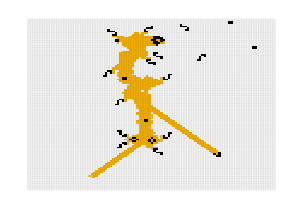

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Silver's reflector"]["MatrixData"],0},{300,{0,100},{100,200}},"Decay"->.999,MeshStyle->Opacity[.06]]
```

and combining them with a hard-to-explain-why-it-works “still life” found by search:

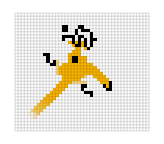

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},{100,{0,35},{0,40}},MeshStyle->Opacity[.1],"Decay"->.98]
```

Another example was the “Sir Robin knightship”---a spaceship that moves like a chess knight 2 cells down and 1 across.  In 2017 a spaceship search found a structure that in 6 steps has many elements that make a knight move---but then subsequently “falls apart”:

```mathematica
GraphicsRow[Append[ArrayPlot[ArrayPad[#,2],Mesh->True,MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife",{SparseArray[…],0},6][[{1,7}]],CellularAutomatonPlot3D["GameOfLife",{SparseArray[…],0},30,ViewPoint->{-1.5100606938664856,-2.9431988487688194,0.712248016806903}]]]
```

-Graphics-

But the next year a carefully orchestrated search was able to “find a tail” that “adds a fix” to this---and successfully produces a final “perfect knightship”:

```mathematica
GraphicsRow[Append[ArrayPlot[ArrayPad[#,2],Mesh->True,MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife",{$LifeData["Sir Robin"]["MatrixData"],0},12][[{5,11}]],CellularAutomatonPlot3D["GameOfLife",{$LifeData["Sir Robin"]["MatrixData"],0},30,ViewPoint->{-1.5100606938664856,-2.9431988487688194,0.712248016806903}]]]
```

-Graphics-

By the way, the idea that one can take something that “almost works” and find a way to “fix it” is one that’s appeared repeatedly in the engineering history of the Game of Life.  At the outset, it’s far from obvious that such a strategy would be viable.  But the fact that it is seems to be similar to the story of why both biological evolution and machine learning are viable---which, as I’ve recently discussed, can be viewed as yet another consequence of the phenomenon of computational irreducibility.

ArrayPlot[$LifeData["Herschel"]["MatrixData"],Mesh->None,Frame->None]

Noted for Arianag/Markl

One thing that’s happened many times in the history of the Game of Life is that at some point some category of structure---like a conduit---is identified, and named.  But then it’s realized that actually there was something that could be seen as an instance of the same category of structure found much earlier, though without the clarity of the later instance, its significance wasn’t recognized.  For example, in 1995 the “Herschel conduit” that moves a  from one position to another (here in 64 steps) was discovered (by a search):

-Graphics-

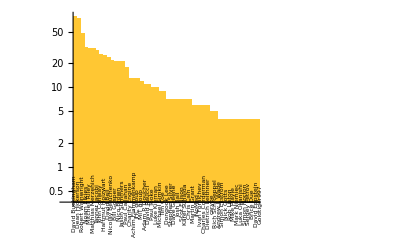

```mathematica
GraphicsRow[{ArrayPlot[ArrayPad[$LifeData["R64"]["MatrixData"],{{1,1},{11,1}}],Mesh->True,MeshStyle->Opacity[.1]],CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["R64"]["MatrixData"],0},64,MeshStyle->Opacity[.1],"Decay"->.95]}]
```

ArrayPlot[{{0,1,0},{0,1,1},{1,1,0}},Mesh->None,Frame->None]

ArrayPlot[{{1,0,0},{0,1,0},{0,1,1},{1,1,0},{1,0,0}},Mesh->None,Frame->None]

Noted for Arianag/Markl

But then it was realized that---if looked at correctly---a similar phenomenon had actually already been seen in 1972, in the form of a structure that in effect takes  if it is present, and “moves it” (in 28 steps) to a  at a different position (albeit with a certain amount of “containable” other activity):

```mathematica
GraphicsRow[{ArrayPlot[ArrayPad[$LifeData["RF28B"]["MatrixData"],{{1,5},{2,3}}],Mesh->True,MeshStyle->Opacity[.1]],CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["RF28B"]["MatrixData"],0},28,MeshStyle->Opacity[.1],"Decay"->.6]},Spacings->30]
```

-Graphics-

Looking at the plots above of new structures found we see the largest peak after 2020.  And, yes, it seems that during the pandemic people spent more time on the Game of Life---in particular trying to fill in tables of structures of particular types, for example, with each possible period.

But what about the human side of engineering in the Game of Life?  The activity brought in people from many different backgrounds.  And particularly in earlier years, they often operated quite independently, and with very different methods (some not even using a computer).  But if we look at all “recorded structures” we can look at when different people contributed, and how many structures in total they contributed:

Colors?
Try scales on top

```mathematica
(*See GoL-10-Data* for retrieval code*) 
namesdiscoverers = Select[, KeyExistsQ[#, "Discovered by"] && StringQ[#[["Discovered by"]] ]&][[All, "Discovered by"]];
```

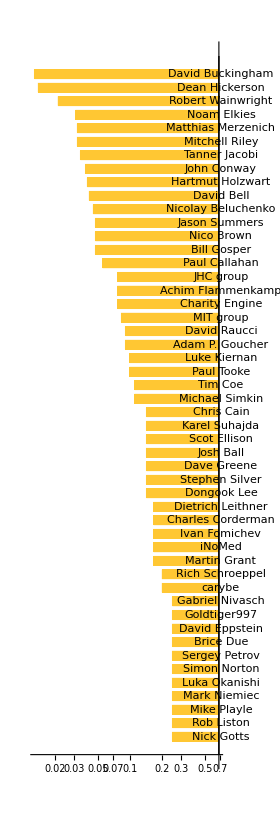
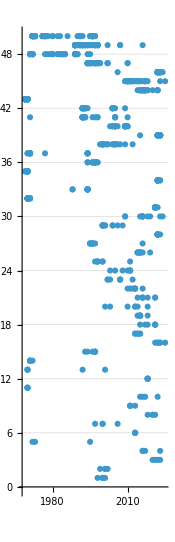

```mathematica
Row[{BarChart[Take[Sort[Counts[namesdiscoverers]],-50], BarOrigin->Right, ScalingFunctions->"Log", AspectRatio->3, ImageSize->280, PlotRangePadding->{Automatic, .8}, ChartLabels->(Style[Text[#],TextAlignment->Center]&)/@Keys[Take[Sort[Counts[namesdiscoverers]],-50]],BarSpacing->Large], ListPlot[{ToExpression[#1],51-#2}&@@@Select[DeleteCases[With[{w=Values[Values/@Select[,KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]]},
Catenate[MapIndexed[Reverse@{First[#2], #1}&,Values[ReverseSortBy[GroupBy[w,First->Last],Length]],{2}]]],{_Missing,_}],#[[2]]<=50&],  AspectRatio->3.1, ImageSize->175,PlotRangePadding->{Automatic, {None, 1.8}}, PlotStyle-> PointSize[.025](*, Frame-> {False, False, True, False}, FrameTicks->Range[1969, 2025]*), Axes->{True, False}, GridLines->{None, Range[.5, 50.5, 1]}]}, Alignment->Top]
```

PM: from Jeremy below

Need a scale for the left part ... e.g. to show it’s logarithmic
On right could try bubbles of different sizes

For Developer

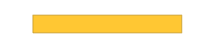
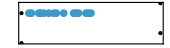
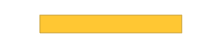
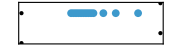
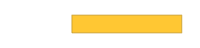
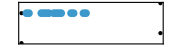
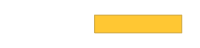
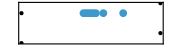
|  | -Graphics-
-Graphics- | David Buckingham | -Graphics-
-Graphics- | Dean Hickerson | -Graphics-
-Graphics- | Robert Wainwright | -Graphics-
-Graphics- | Noam Elkies | -Graphics-
-Graphics- | Mitchell Riley | -Graphics-
-Graphics- | Matthias Merzenich | -Graphics-
-Graphics- | Tanner Jacobi | -Graphics-
-Graphics- | John Conway | -Graphics-
-Graphics- | Hartmut Holzwart | -Graphics-
-Graphics- | David Bell | -Graphics-
-Graphics- | Nicolay Beluchenko | -Graphics-
-Graphics- | Nico Brown | -Graphics-
-Graphics- | Jason Summers | -Graphics-
-Graphics- | Bill Gosper | -Graphics-
-Graphics- | Paul Callahan | -Graphics-
-Graphics- | JHC group | -Graphics-
-Graphics- | Charity Engine | -Graphics-
-Graphics- | Achim Flammenkamp | -Graphics-
-Graphics- | MIT group | -Graphics-
-Graphics- | David Raucci | -Graphics-
-Graphics- | Adam P. Goucher | -Graphics-
-Graphics- | Paul Tooke | -Graphics-
-Graphics- | Luke Kiernan | -Graphics-
-Graphics- | Tim Coe | -Graphics-
-Graphics- | Michael Simkin | -Graphics-
-Graphics- | Stephen Silver | -Graphics-
-Graphics- | Scot Ellison | -Graphics-
-Graphics- | Karel Suhajda | -Graphics-
-Graphics- | Josh Ball | -Graphics-
-Graphics- | Dongook Lee | -Graphics-
-Graphics- | Dave Greene | -Graphics-
-Graphics- | Chris Cain | -Graphics-
-Graphics- | Martin Grant | -Graphics-
-Graphics- | Ivan Fomichev | -Graphics-
-Graphics- | iNoMed | -Graphics-
-Graphics- | Dietrich Leithner | -Graphics-
-Graphics- | Charles Corderman | -Graphics-
-Graphics- | Rich Schroeppel | -Graphics-
-Graphics- | carybe | -Graphics-
-Graphics- | Simon Norton | -Graphics-
-Graphics- | Simon Ekström | -Graphics-
-Graphics- | Sergey Petrov | -Graphics-
-Graphics- | Rob Liston | -Graphics-
-Graphics- | Nick Gotts | -Graphics-
-Graphics- | Mike Playle | -Graphics-
-Graphics- | Mark Niemiec | -Graphics-
-Graphics- | Luka Okanishi | -Graphics-
-Graphics- | Goldtiger997 | -Graphics-
-Graphics- | Gabriel Nivasch | -Graphics-
-Graphics- | David Eppstein | -Graphics-

```mathematica
discoveries=Take[SortBy[GroupBy[
Values[Values/@Select[,KeyExistsQ[#,"Discovered by"]&&StringQ[#[["Discovered by"]]]&][[All,{"Discovered by","Year of discovery"}]]],First->Last],Length],-50];
Grid[{{Null,Null,Graphics[{},AspectRatio->.06,PlotRange->{{1969,2025},Automatic},
ImageSize->170,Axes->{True,False},AxesStyle->White,
TicksStyle->White,LabelStyle->GrayLevel[.5],ImageMargins->{{0,0},{5,0}}]}} ~Join~
Map[{
Item[BarChart[{Length[#[[2]]]^.6}, BarOrigin->Right,AspectRatio->.05, ChartStyle->EdgeForm[Hue[0.12091505713081323, 0.8000000035401837, 0.76]],
PlotRangePadding->{.05, .0},Axes->False,PlotRange->{{0,15},{0,2}},ImageSize->200],Alignment->Top],
Item[Style[#[[1]],"Label"],Alignment->Top],
TimelinePlot[DeleteDuplicates[DeleteMissing[#[[2]]]],Axes->False,
AspectRatio->.06,PlotRange->{{1969},{2025}},ImageSize->170,PlotMarkers->{Automatic,8},
Frame->{{False,False},{True,False}},FrameTicks->False,FrameStyle->GrayLevel[.85]]
}&,Reverse[Normal[discoveries]]],Alignment->{Left,Bottom},Spacings->{.5,0}]
```

Needless to say---given that we’re dealing with an almost-60-year span---different people tend to show up as active in different periods.  Looking at everyone, there’s a roughly exponential distribution to the number of (named) structures they’ve contributed.  (Though note that the very top contributors shown here found parametrized collections of structures and then recorded many instances.)

## The Example of Oscillators

As a first example of systematic “innovation history” in the Game of Life let’s talk about oscillators.  Here are the periods of oscillators that were found up to 1980:

Figure out how to remove the “headroom”

```mathematica
progress =Module[{sorted = SortBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 30}]];
```

```mathematica
ListPlot[
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress[[All,1]]], PlotStyle->Directive[Red, PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@Select[progress[[All, 1]],#Year<1981&]}), PlotRange->{{1969, 1981}, {0, 30}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

PM: from Willem below

```mathematica
progress =Module[{sorted = SortBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 30}]];
```

```mathematica
ListPlot[
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress[[All,1]]], PlotStyle->Directive[Red, PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@Select[progress[[All, 1]],#Year<1981&]}), PlotRange->{{1969, 1981}, {0, 30}}, AspectRatio->.4, Frame-> True, PlotRangePadding->{0, {0, 1.5}}]
```

-Graphics-

As of 1980, many periods were missing.  But in fact all periods are possible---though it wasn’t until 2023 that they were all filled in:

```mathematica
ListPlot[
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress[[All,1]]], PlotStyle->Directive[Red, PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, 1]]}), PlotRange->{{1969, 2025}, {0, 30}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

PM: from Willem below

```mathematica
ListPlot[
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress[[All,1]]], PlotStyle->Directive[Red, PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, 1]]}), PlotRange->{{1969, 2025}, {0, 30}}, AspectRatio->.4, Frame-> True, PlotRangePadding->{0, {0, 1.5}}]
```

-Graphics-

And if we plot the number of distinct periods (say below 60) found by a given year, we can get a first sense of the “arc of progress” in “oscillator technology” in the Game of Life:

```mathematica
ListStepPlot[With[{ys={#Period,#Year}&/@With[{o=Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&]},Table[First@MinimalBy[Select[o,#Period===p&],#Year&,1],{p,2,60}]]},Table[{y,Count[Last/@ys,x_/;x<=y]},{y,1969,2025}]],Frame->True,AspectRatio->.4,Filling->Axis,FrameLabel->{Automatic,"number of periods found"}]
```

-Graphics-

Finding an oscillator of a given period is one thing.  But how about the smallest oscillator of that period?  We can be fairly certain that not all of these are known, even for periods below 30.  But here’s a plot that shows when the progressive “smallest so far” oscillators were found for a given period:

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, -1]]}), PlotRange->{{1969, 2025}, {0, 30}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

PM: from Willem below

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, -1]]}), PlotRange->{{1969, 2025}, {0, 30}}, AspectRatio->.4, Frame-> True, PlotRangePadding->{0, {0, 1.5}}]
```

-Graphics-

And here’s the corresponding plot for all periods up to 100:

Try to get to 100

```mathematica
progress =Module[{sorted = SortBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 60}]];
```

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.0075]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, -1]]}), PlotRange->{{1969, 2025}, {0, 60}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

PM: from Willem below

```mathematica
progress2 =DeleteCases[Module[{curr, weightsovertime,improvements,locs, sorted},
Table[
sorted = Catenate[
ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@ 
GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==i&],#Year&], #Year&]
];
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 100}]], {}];
```

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress2, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.0075]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress2[[All, -1]]}), PlotRange->{{1969, 2025}, {0, 100}}, AspectRatio->.4, Frame-> True, PlotRangePadding->{0, {0,3}}]
```

-Graphics-

But what about the actual reduction in size that’s achieved?  Here’s a plot for each oscillator period showing the sequence of sizes found---in effect the “arc of engineering optimization” that’s achieved:

Possible label the end of each line with its period [ ? ]

For Developer

```mathematica
ListLinePlot[Callout[Style[{#Year,Times@@Dimensions[#MatrixData]}],ArrayPlot[ArrayPad[#MatrixData,1],ImageSize->Tiny]]&/@#&/@Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]],{i,2,50}],PlotStyle->PointSize[.01],PlotRange->All,AspectRatio->.4,Frame->True,FrameLabel->{None,"area"},PlotRangePadding->{{.2,.2},Automatic}]
```

-Graphics-

Consider 3D version

For Developer (done below?)

```mathematica
ListLinePlot3D[Callout[Style[{#Year,#Period,Times@@Dimensions[#MatrixData]}],ArrayPlot[ArrayPad[#MatrixData,1],ImageSize->Tiny]]&/@#&/@Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]],{i,2,50}],PlotStyle->PointSize[.01],PlotRange->All,AxesLabel->{None,"period","area"},Mesh->True,BoxRatios->{2,1,.6},Filling->Axis,ScalingFunctions->{None,None,{Sqrt,#^2&}}]
```

-Graphics3D-

So what are the actual patterns associated with these various oscillators?  Here are some results (with blue dots indicating on a timeline the date when each pattern was found):

Make the numbers into callouts on the number lines
Use total number that balances columns best

Fix broken number
Try to line up baselines of numbers

For Developer

```mathematica
Row[Column[Table[Module[{weightsovertime,improvements,locs,p=i,byyear},byyear=Catenate[ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&],#Year&]];
weightsovertime=Times@@Dimensions[#MatrixData]&/@byyear;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[Column[{GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,ImageSize->3 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@byyear[[locs]]],NumberLinePlot[Callout[#Year,#Year]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]],Axes->None,PlotRange->{1968,2025}]}],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{Range[2,12],Range[13,21]},Spacer[15]]
```

-Graphics-
-Graphics-period 2  
-Graphics-
-Graphics-period 3  
-Graphics-
-Graphics-period 4  
-Graphics-
-Graphics-period 5  
-Graphics-
-Graphics-period 6  
-Graphics-
-Graphics-period 7  
-Graphics-
-Graphics-period 8  
-Graphics-
-Graphics-period 9  
-Graphics-
-Graphics-period 10  
-Graphics-
-Graphics-period 11  
-Graphics-
-Graphics-period 12  -Graphics-
-Graphics-period 13  
-Graphics-
-Graphics-period 14  
-Graphics-
-Graphics-period 15  
-Graphics-
-Graphics-period 16  
-Graphics-
-Graphics-period 17  
-Graphics-
-Graphics-period 18  
-Graphics-
-Graphics-period 19  
-Graphics-
-Graphics-period 20  
-Graphics-
-Graphics-period 21

But how were these all found?   The period 2 “blinker” was very obvious---showing up in evolution from almost any random initial condition.  Some other oscillators were also easily found by looking at the evolution of particular, simple initial conditions.  For example, a line of 10 black cells after 3 steps gives the period-15 “pentadecathlon”.  Similarly, the period-3 “pulsar” emerges from a pair of length-5 blocks after 22 steps:

```mathematica
GraphicsGrid[Partition[ArrayPlot/@CellularAutomaton["GameOfLife",{{Join[Table[1,5],{0},Table[1,5]]},0},30],15]]
```

-Graphics-

Many early oscillators were found by iterative experimentation, often starting with stable “still life” configurations, then perturbing them slightly, as in this period-4 case:

```mathematica
GraphicsRow[{GraphicsRow[ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife",{{{0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,1,1,0,0,0,0},{1,1,0,1,0,0,0,0,1,0,0,0},{1,1,0,1,0,1,1,0,1,0,0,0},{0,0,0,1,0,1,1,0,1,0,1,1},{0,0,0,1,0,0,0,0,1,0,1,1},{0,0,0,0,1,1,1,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0},{0,0,0,0,1,1,0,0,0,0,0,0}},0},4]],GraphicsRow[ArrayPlot[ArrayPad[#,1],Mesh->True,MeshStyle->Opacity[.1]]&/@CellularAutomaton["GameOfLife",{$LifeData["Pinwheel"]["MatrixData"],0},4]]}]
```

-Graphics-

ArrayPlot[$LifeData["Eater 1"]["MatrixData"],Mesh->True,Frame->False]

ArrayPlot[$LifeData["Block"]["MatrixData"],Mesh->True,Frame->False]

Noted for Arianag/Markl

Another common strategy for finding oscillators was to take an “unstable” configuration, then to “stabilize” it by putting “robust” still lifes such as the “block”  or the “eater”  around it---yielding results like:

```mathematica
GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData[#]["MatrixData"],0},$LifeData[#]["Period"]],Text[StringTemplate["period ``"][$LifeData[#]["Period"]]]]&/@{"Unix","Worker bee","Dinner table"},Spacings->20]
```

-Graphics-

For periods that can be formed as LCMs of smaller periods one “construction-oriented” strategy has been to take oscillators with appropriate smaller periods, and combine them, as in:

```mathematica
GraphicsRow[{GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{First[#],0},Last[#],ImageSize->6Last[Dimensions[First[#]]]],Text[StringTemplate["period ``"][Last[#]]]]&/@{{Last[CellularAutomaton["GameOfLife",{Reverse/@$LifeData["Mold"]["MatrixData"],0},9]],4},
{Last[CellularAutomaton["GameOfLife",{Reverse/@Transpose[$LifeData["Fire-spitting"]["MatrixData"]],0},9]],3},
{Last[CellularAutomaton["GameOfLife",{$LifeData["Mold on fire-spitting"]["MatrixData"],0},9]],12}}],GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{First[#],0},Last[#],ImageSize->6Last[Dimensions[First[#]]]],Text[StringTemplate["period ``"][Last[#]]]]&/@{{Reverse/@Last[CellularAutomaton["GameOfLife",{$LifeData["Caterer"]["MatrixData"],0},8]],3},{Last[CellularAutomaton["GameOfLife",{$LifeData["Figure eight"]["MatrixData"],0},7]],8},{Last[CellularAutomaton["GameOfLife",{Transpose[ImportString["x=6,y=18,rule=B3/S23
bo$obo2$2bo$b2o$b5o$b2ob2o$2bo5$3o$3o$3o$3b3o$3b3o$3b3o!","RLE"]],0},6]],24}}]},Spacings->40]
```

-Graphics-

In general, many different strategies have been used, as indicated for example by the sequence of period 3 oscillators that have been recorded over the years (where “smallest-so-far” cases are highlighted):

```mathematica
Module[{p3=SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==3&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]];
Row[Values[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},6,MeshStyle->Opacity[.07],ImageSize->11 Sqrt[1+Last[Dimensions[#MatrixData]]],Frame->MemberQ[improvements,#],FrameStyle->Directive[Red,Thickness[.05]]],Text[Style[#Year,9,Gray]]]&/@p3],Spacer[1]]]
```

-Graphics-1970-Graphics-1970-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1973-Graphics-1973-Graphics-1973-Graphics-1977-Graphics-1982-Graphics-1985-Graphics-1988-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1990-Graphics-1993-Graphics-1993-Graphics-1993-Graphics-1993-Graphics-1994-Graphics-1997-Graphics-2003-Graphics-2012-Graphics-2017-Graphics-2018-Graphics-2021-Graphics-2022

By the mid-1990s oscillators of many periods had been found.  But there were still holdouts, like period 19 and for example pretty much all periods between 61 and 70 (except, as it happens, 66).   At the time, though, all sorts of complicated constructions---say of prime generators---were nevertheless being done.  And in 1996 it was figured out that one could in effect always “build a machine” (using only structures that had already been found two decades earlier) that would serve as an oscillator of any (sufficiently large) period (here 67)---effectively by “sending a signal around a loop of appropriate size”:

```mathematica
GraphicsRow[{CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["p67 Herschel loop"]["MatrixData"],0},67,"Decay"->.95,Mesh->None,ImageSize->{Automatic,250}],CellularAutomatonPlot3D["GameOfLife",{$LifeData["p67 Herschel loop"]["MatrixData"],0},2 67,ViewPoint->{2.716721076863372,-1.995782064969705,0.2937354926997763},ImageSize->{Automatic,280}],CellularAutomatonSpacetimePlot["GameOfLife",{$LifeData["p67 Herschel loop"]["MatrixData"],0},67 2,"Decay"->.9,Mesh->None,ImageSize->{Automatic,280}]},Spacings->50]
```

-Graphics-

But by the 2010s, with large numbers of fast computers becoming available, there was again an emphasis on pure random search.  A handful of highly efficient programs were developed, that could be run on anyone’s machine.  In typical case, a search might consist of starting, say, from a trillion randomly chosen initial conditions (or “soups”), identifying new structures that emerge, then seeing whether these act, for example, as oscillators.  Typically any new discovery was immediately reported in online forums---leading to variations of it being tried, and new follow-on results often being reported within hours or days.

Many of the random searches started just from 16×16 regions of randomly chosen cells (or larger regions with symmetries imposed).  And in a typical manifestation of computational irreducibility, many surprisingly small and “randomly looking” (at least up to symmetries) results were found.  So, for example, here’s the sequence of recorded period-16 oscillators with smaller-than-before cases highlighted:

```mathematica
Module[{p3=Drop[SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==16&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],{-2}],improvements},improvements=Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]];
Row[Values[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16,MeshStyle->Opacity[.07],ImageSize->14 Sqrt[1+Last[Dimensions[#MatrixData]]],Frame->MemberQ[improvements,#],FrameStyle->Directive[Red,Thickness[.05]]],Text[Style[#Year,9,Gray]]]&/@p3],Spacer[1]]]
```

-Graphics-1983-Graphics-1984-Graphics-1994-Graphics-1994-Graphics-1994-Graphics-2016-Graphics-2018-Graphics-2020-Graphics-2022-Graphics-2022-Graphics-2022-Graphics-2023

Up through the 1990s results were typical found by a mixture of construction and small-scale search.  But in 2016, results from large-scale random searches (sometimes symmetrical, sometimes not) started to appear.

The contrast between construction and search could be dramatic, like here for period 57:

```mathematica
GraphicsRow[Values[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#["MatrixData"],0},57,"Decay"->.9,MeshStyle->Opacity[.1],Mesh->Length[#["MatrixData"]]<50,ImageSize->50Length[#["MatrixData"]]^.2],Text[Style[#Year,9,Gray]]]&/@Take[Quiet[Select[$LifeData,#Class==="Oscillator"&&#Period===57&]],2]],Spacings->40]
```

-Graphics-

One might wonder whether there could actually be a systematic, purely algorithmic way to find, say, possible oscillators of a given period.  And indeed for one-dimensional cellular automata (as I noted in 1984), it turns out that there is.  Say one considers blocks of cells of width w.  Which block can follow which other is determined by a de Bruijn graph, or equivalently, a finite state machine.  If one is going to have a pattern with period p, all blocks that appear in it must also be periodic with period p.  But such blocks just form a subgraph of the overall de Bruijn graph, or equivalently, form another, smaller, finite state machine.  And then all patterns with period p must correspond to paths through this subgraph.  But how long are the blocks one has to consider?

In 1D cellular automata, it turns out that there’s an upper bound of 2^(2p).  But for 2D cellular automata---like the Game of Life---there is in general no such upper bound, a fact related to the undecidability of the 2D tiling problem.  And the result is that there’s no complete, systematic algorithm to find oscillators in a general 2D cellular automaton, or presumably in the Game of Life.

But---as was actually already realized in the mid-1990s---it’s still possible to use algorithmic methods to “fill in” pieces of patterns.  The idea is to define part of a pattern of a given period, then use this as a constraint on filling in the rest of it, find “solutions” that satisfy this constraints using SAT solving techniques.  In practice, this approach has more often been used for spaceships than for oscillators (not least because it’s only practical for small periods).  But one feature of it is that it can generate fairly large patterns with a given period.

Yet another method that’s been tried has to generate oscillators by colliding gliders in many possible ways.  But while this is definitely useful if one’s interested in what can be made using gliders, it doesn’t seem to have, for example, allowed people to find much in the way of interesting new oscillators.

## Modularity

In traditional engineering a key strategy is modularity.  Rather than trying to build something “all in one go”, the idea is to build a collection of independent subsystems, from which the whole system can then be assembled.  But how does this work in the Game of Life?  We might imagine that to identify the modular parts of a system, we’d have to know the “process” by which the system was put together, and the “intent” involved.  But because in the Game of Life we’re ultimately just dealing with pure patterns of bits we can in effect just as well “come in at the end” and algorithmically figure out what pieces are operating as separate, modular parts.

ArrayPlot[Table[0,3,3],Mesh->True,ImageSize->20]

Noted for Arianag/Markl

So how can we do this?  Basically what we want to find out is which parts of a pattern “operate independently” at a given step, in the sense that these parts don’t have any overlap in the cells they affect.  Given that in the rules for the Game of Life a particular cell can affect any of the 9 cells in its  neighborhood, we can say that black cells can only have “overlapping effects” if they are at most 2 √2 cell units apart.   So then we can draw a “nearest neighbor graph” that shows which cells are connected in this sense:

Make pictures better

```mathematica
mmm=ArrayPad[Normal[$LifeData["Worker bee"]["MatrixData"]],1];
```

```mathematica
With[{g=NearestNeighborGraph[Position[Transpose[
Reverse[#]],1], {All,2Sqrt[2]}]},ArrayPlot[#,Mesh->True,MeshStyle->Opacity[.2],ColorRules->{1->Gray},Epilog->Style[Line[List@@#-.5]&/@EdgeList[Graph[g,VertexCoordinates->Thread[VertexList[g]->VertexList[g]]]],Thick,Red]]]&/@CellularAutomaton["GameOfLife",mmm,2]
```

{-Graphics-,-Graphics-,-Graphics-}

PM: from Jeremy below: “Changed gray color and made the lines a bit thinner”

```mathematica
mmm=ArrayPad[Normal[$LifeData["Worker bee"]["MatrixData"]],1];
```

```mathematica
With[{g=NearestNeighborGraph[Position[Transpose[
Reverse[#]],1], {All,2Sqrt[2]}]},ArrayPlot[#,Mesh->True,MeshStyle->Opacity[.2],ColorRules->{1->Hue[0.56, 0.29, 0.73]},Epilog->Style[Line[List@@#-.5]&/@EdgeList[Graph[g,VertexCoordinates->Thread[VertexList[g]->VertexList[g]]]],AbsoluteThickness[1.5],Red]]]&/@CellularAutomaton["GameOfLife",mmm,2]
```

{-Graphics-,-Graphics-,-Graphics-}

But what about the whole evolution?  We can draw what amounts to a causal graph that shows the causal connections between the “independent modular parts” that exist at each step:

Line up LHS and RHS columns
Increase size of vertices on RH column
Possibly put low opacity horizontal guide lines

```mathematica
GraphicsRow[{GraphicsColumn[With[{g=NearestNeighborGraph[Position[Transpose[
Reverse[#]],1], {All,2Sqrt[2]}]},ArrayPlot[#,Mesh->True,MeshStyle->Opacity[.2],ColorRules->{1->Gray},Epilog->Style[Line[List@@#-.5]&/@EdgeList[Graph[g,VertexCoordinates->Thread[VertexList[g]->VertexList[g]]]],Thick,Red]]]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 9]],GraphPlot[PatternsLayeredGraph[$LifeData["Worker bee"]],ImageSize-> {375, Automatic}]},Spacings->20]
```

-Graphics-

PM: from Willem below, “Increased vertex size, made arrows visible, lined up steps, divider lines are going to have to be  hacky because graphics row doesn’t let me adjust the size of the graph so waiting on those.” Will also need to change the gray color (ColorRules->{1->Hue[0.56, 0.29, 0.73]}) and make the lines a bit thinner (AbsoluteThickness[1.5],Red), as provided by Jeremy

```mathematica
Row[{GraphicsColumn[With[{g=NearestNeighborGraph[Position[Transpose[
Reverse[#]],1], {All,2Sqrt[2]}]},ArrayPlot[#,Mesh->True,MeshStyle->Opacity[.2],ColorRules->{1->Gray},Epilog->Style[Line[List@@#-.5]&/@EdgeList[Graph[g,VertexCoordinates->Thread[VertexList[g]->VertexList[g]]]],Thick,Red]]]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 9], ImageSize->60],(*Rasterize[*)GraphPlot[PatternsLayeredGraph[$LifeData["Worker bee"], Automatic, "VertexSizeFunction"-> (4Dimensions[#]&), ImageSize-> 240], PlotRangePadding->{Automatic, {0,1}}](*]*)
}, Spacer[10]]
```

-Graphics--Graphics-

And given this, we can summarize the “modular structure” of this particular oscillator by the causal graph:

```mathematica
BoundingBoxLayeredGraph[$LifeData["Worker bee"]]
```

-Graphics-

Ultimately all that matters in the “overall operation” of the oscillator is the partial ordering defined by this graph.  Parts that appear “horizontally separated” (or, more precisely, in antichains, or in physics terminology, spacelike separated) can be generated independently and in parallel.  But parts that follow each other in the partial order need to be generated in that order (i.e. tin physics terms, they are timelike separated).

As another example, let’s look at graphs for the various oscillators of period 16 that we showed above:

Clean up
Include the years here

```mathematica
GraphicsRow[Column[{BoundingBoxLayeredGraph[#],CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16,ImageSize->12 Sqrt[Last[Dimensions[#MatrixData]]]]},Center]&/@SortBy[allimps[[15]],#Year&],Frame->All,FrameStyle->Opacity[.2],Spacings->30]
```

-Graphics-

PM: from Willem below

```mathematica
Grid[{
Style[Text[#Year], 11]&/@SortBy[allimps[[15]],#Year&],
Column[{
BoundingBoxLayeredGraph[#, Automatic(*, ImageSize->{125, 210} *)(*PlotRange-> {{-15, 8}, Automatic}*)],CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16, ImageSize->{90, 75}
(*6 Sqrt[Last[Dimensions[#MatrixData]]]*)(*{75, 50}*)]}, Spacings->{0,1.5},Alignment->Center] &/@SortBy[allimps[[15]],#Year&]},(*Frame->{None, Automatic},*)FrameStyle->Opacity[.2],Dividers->{All, {True, False, True}}, Alignment->Center, Spacings->{1, 1.5}]
```

1983 | 1994 | 1994 | 2016 | 2020
-Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics-

What we see is that the early period-16 oscillators were quite modular, and had many parts that in effect operated independently.  But the later, smaller ones were not so modular.  And indeed the last one shown here had no parts that could operate independently; the whole pattern had to be taken together at each step.

And indeed, what we’ll often see is that the more optimized a structure is, the less modular it tends to be.  If we’re going to construct something “by hand” we usually need to assemble it in parts, because that’s what allows us to “understand what we’re doing”.  But if, for example, we just find a structure in a search, there’s no reason for it to be “understandable”, and there’s no reason for it to be particularly modular.

Different steps in a given oscillator can involve different numbers of modular parts.  But as a simple way to assess the “modularity” of an oscillator, we can just ask for the average number of parts over the course of one period.  So as an example, here are the results for period-30 oscillators:

Clean up

For Developer

```mathematica
GraphicsRow[Values[Column[{BoundingBoxLayeredGraph[#],Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16,ImageSize->12 Sqrt[Last[Dimensions[#MatrixData]]]],Column[{#Year,N[VertexCount[BoundingBoxLayeredGraph[#,#Period-1]]/#Period,2]}]]},Center]&/@SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==30&]//Quiet,#Year&]],Frame->All,FrameStyle->Opacity[.2],Spacings->30]
```

-Graphics-

And we can see that cases found by searches tend to have smaller “modularity indices” than ones that were explicitly constructed.

As

Color the dots by  red=first of each period, blue=smallest, gray=in between

```mathematica
allimps = Table[Module[{p3=SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==i&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]]],{i, 2,60}];
```

```mathematica
ListPointPlot3D[Map[{#Year,#Period, VertexCount[BoundingBoxLayeredGraph[#,#Period-1]]/#Period}&,  Take[allimps,40],{2}],Filling->Axis,BoxRatios->{1,1,.6},AxesLabel->{None,"period","modularity index"},PlotRange->All]
```

-Graphics3D-

PM: done below

```mathematica
ListPointPlot3D[Map[With[{l=Length[#]},MapIndexed[Style[{#Year,#Period, VertexCount[BoundingBoxLayeredGraph[#,#Period-1]]/#Period},If[First[#2]==1,Red,If[First[#2]==l,Blue,Gray]]]&,  #]]&,Take[allimps,40]],Filling->Axis,BoxRatios->{1,1,.6},AxesLabel->{None,"period","modularity index"},PlotRange->All]
```

-Graphics3D-

```mathematica
ListLinePlot3D[Map[With[{l=Length[#]},MapIndexed[Style[{#Year,#Period, VertexCount[BoundingBoxLayeredGraph[#,#Period-1]]/#Period},If[First[#2]==1,Red,If[First[#2]==l,Blue,Gray]]]&,  #]]&,Take[allimps,40]],Filling->Axis,BoxRatios->{1,1,.6},AxesLabel->{None,"period","modularity index"},PlotRange->All,Mesh->All]
```

-Graphics3D-

## Gliders & Spaceships

Oscillators are structures that cycle but do not move.  “Gliders” and, more generally, “spaceships” are structures that move every time they cycle.  When the Game of Life was first introduced, four examples of these (all of period 4) were found almost immediately (the last one being the result of trying to extend the one before it):

Clean up

For Developer

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{If[# === "Glider", Identity, (Reverse/@#&)][$LifeData[#]["MatrixData"]],0},16,"Margin"-> 1,ImageSize->{Automatic,60}]&/@{"Glider","Lightweight spaceship","Middleweight spaceship","Heavyweight spaceship"}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Within a couple of years, experimentation had revealed two variants, with periods 12 and 20 respectively, involving additional structures:

```mathematica
GraphicsGrid[Transpose[{CellularAutomatonHistoryPlot["GameOfLife",{CellularAutomaton["GameOfLife",{Reverse/@$LifeData[#]["MatrixData"],0},{{{6}}}],0},30,"Margin"-> 3,ImageSize->220]&/@{"Ecologist","Schick engine"},CellularAutomatonPlot3D["GameOfLife",{CellularAutomaton["GameOfLife",{Reverse/@$LifeData[#]["MatrixData"],0},{{{6}}}],0},60,ImageSize->{Automatic,220}]&/@{"Ecologist","Schick engine"},CellularAutomatonSpacetimePlot["GameOfLife",{CellularAutomaton["GameOfLife",{Reverse/@$LifeData[#]["MatrixData"],0},{{{6}}}],0},60,ImageSize->{Automatic,200}]&/@{"Ecologist","Schick engine"}}],Spacings->25]
```

-Graphics-

But after that, for nearly two decades, no more spaceships were found.  In 1989, however, a systematic method for searching was invented, and in the years since, a steady stream of new spaceships have been found.  A variety of different periods have been seen

Add pattern callout
Possibly add horizontal guides

For Developer

```mathematica
With[{data=Values[{#Year,#Period}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[Catenate[MapAt[Style[#,Red]&,#,1]&/@GatherBy[data,Last]],Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,PlotRange->All,ScalingFunctions->"Log"]]
```

-Graphics-

as well as a variety of speeds (and three different angles):

Fix y scale labels have √□ symbols
Add back in colors
Add pattern callouts
Line up dots and arrows

For Developer

```mathematica
as =
Map[
If[Times@@Dimensions[#MatrixData]<10000,If[MemberQ[#,0],-Pi/2,If[Abs[#[[1]]/#[[2]]]==1,-Pi/4,-ArcTan[1/2]]]&[getvector[#]],0] &,Values[Select[$LifeData,#Class==="Spaceship"&]]];
```

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[Tooltip[{#Year,Norm[#Speed]},If[Times@@Dimensions[#MatrixData]>5000, "Too large",CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, Min[5#Period, 100]]]]& ,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,InputForm[#]}&/@Union[Last/@data],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle-> RGBColor[0.27, 0.63, 1],PlotMarkers->({Rotate[Graphics[{{AbsolutePointSize[8],Opacity[.2],Point[{0,0}]},Style[Text[Style["⟶",Bold,11],{0,0}],GrayLevel[.3]]}],#+Pi/2], 30}&/@as)]]
```

-Graphics-

```mathematica
With[{data=Values[{#Year,Norm[#Speed]}&/@Select[$LifeData,#Class==="Spaceship"&]]},ListPlot[
List/@Catenate[
MapAt[Style[#,Red]&,#,1]&/@
Map[Tooltip[{#Year,Norm[#Speed]},If[Times@@Dimensions[#MatrixData]>5000, "Too large",CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, Min[5#Period, 100]]]]& ,GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&]],
#Speed&], {2}]],
Frame->True,FrameLabel->{None,"speed (cells/step)"},FrameTicks->{{{#,InputForm[#]}&/@Union[Last/@data],None},{Automatic,None}},AspectRatio->.4,PlotRange->{0,.55},PlotStyle-> RGBColor[0.27, 0.63, 1],PlotMarkers->({Rotate[Graphics[{{AbsolutePointSize[4],Point[{0,0}]},Style[Text[Style["⟶",Bold,11],{0,0}],GrayLevel[.3]]}],#], 30}&/@as)]]
```

-Graphics-

The forms of these spaceships are quite diverse:

Indicate with arrows e.g.  period 4↘  direction

Break this apart for both period and direction   [[[ NOTE: make sure it’s the full discovery sequence ]]]

PM: done below?

```mathematica
bydirperiod=SortBy[(SortBy[#,#Year&]&/@GatherBy[Values[Select[$LifeData,#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&&2<=#[["Period"]]<60&]],{#Period,Sort[Abs[getvector[#]]]}&]),#[[1,"Period"]]&];
```

```mathematica
getinitialangle[vec_]:=If[MemberQ[vec,0],0,If[Abs[vec[[1]]/vec[[2]]]==1,-Pi/4,ArcTan[1/2]]]
```

```mathematica
caption[per_,sp_,ang_]:=Column[{Text[Style[Row[{Style["period ",9],per}],10]],Text[Style[Row[{Style["speed ",9],sp," ",Rotate["→",ang]}],10]]}]
```

```mathematica
Style[Row[Labeled[GraphicsRow[Labeled[Rotate[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,PlotRangePadding->{0,0},ImageSize->{{30,12 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]]^.5}},Mesh->True,MeshStyle->Opacity[(.5/(Times@@Dimensions[#MatrixData])^.4)]],With[{vec=getvector[#]},getangle[vec]+If[SameQ@@Abs[vec],0,Pi/2]]],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@# (*ImageSize->{{20,300},{10,100}}*)],caption[#[[1]]["Period"],#[[1]]["Speed"],getinitialangle[getvector[#[[1]]]]],Left]&/@(DeleteDuplicates[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],#]]&/@#)&[bydirperiod],Graphics[Style[Line[{{0,-1},{0,1}}],GrayLevel[.8]],PlotRange->{{-.1,.1},{-1,1}},ImageSize->{12,60}]],LineSpacing->{1,1}]
```

-Graphics--Graphics-period 2
speed 1/2 →-Graphics-period 3
speed 1/3 →-Graphics-period 4
speed 1/4 →-Graphics-period 4
speed 1/2 →-Graphics-period 4
speed 1/4 →-Graphics-period 5
speed 1/5 →-Graphics-period 5
speed 1/5 →-Graphics-period 5
speed 2/5 →-Graphics-period 6
speed 1/3 →-Graphics-period 6
speed 1/2 →-Graphics-period 6
speed 1/6 →-Graphics-period 6
speed {1/3,1/6} →-Graphics-period 6
speed 1/6 →-Graphics-period 7
speed 1/7 →-Graphics-period 7
speed 2/7 →-Graphics-period 7
speed 1/7 →-Graphics-period 7
speed 3/7 →-Graphics-period 8
speed 1/4 →-Graphics-period 8
speed 1/8 →-Graphics-period 8
speed 1/2 →-Graphics-period 9
speed 1/3 →-Graphics-period 10
speed 1/5 →-Graphics-period 10
speed 1/10 →-Graphics-period 12
speed 1/2 →-Graphics-period 15
speed 1/5 →-Graphics-period 16
speed 1/2 →-Graphics-period 20
speed 1/2 →-Graphics-period 21
speed 2/7 →-Graphics-period 30
speed 1/5 →-Graphics-period 36
speed 1/2 →

Some are “tightly integrated”, while some have many “modular pieces”, as revealed by their causal graphs:

Clean up

For Developer

```mathematica
Row[Column[Table[Module[{weightsovertime,improvements,locs,p=i,byyear},byyear=Catenate[ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&],#Year&]];
weightsovertime=Times@@Dimensions[#MatrixData]&/@byyear;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[Column[{GraphicsRow[Labeled[BoundingBoxLayeredGraph[#,#Period,ImageSize->{Automatic,140}],Text[Style[#Year,9,GrayLevel[.3]]],BaselinePosition->Top]&/@byyear[[locs]]],NumberLinePlot[Callout[#Year,#Year]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Spaceship"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]],Axes->None,PlotRange->{1968,2025}]}],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{{2,3,4,5,6,7,8,9,10},{12,15,16,20,21,30,36}},Spacer[15]]
```

-Graphics-
-Graphics-period 2  
-Graphics-
-Graphics-period 3  
-Graphics-
-Graphics-period 4  
-Graphics-
-Graphics-period 5  
-Graphics-
-Graphics-period 6  
-Graphics-
-Graphics-period 7  
-Graphics-
-Graphics-period 8  
-Graphics-
-Graphics-period 9  
-Graphics-
-Graphics-period 10  -Graphics-
-Graphics-period 12  
-Graphics-
-Graphics-period 15  
-Graphics-
-Graphics-period 16  
-Graphics-
-Graphics-period 20  
-Graphics-
-Graphics-period 21  
-Graphics-
-Graphics-period 30  
-Graphics-
-Graphics-period 36

Period 96 spaceships provide an interesting example of the “arc of progress” in the Game of Life.  Back in 1971, a systematic enumeration of small polyominoes was done, looking for one that could “reproduce itself”.  While no polyomino on its own seemed to do this, a case was found where part of the pattern produced after 48 steps seemed to reappear repeatedly every 48 steps thereafter:

Burn in these heights

For Developer

```mathematica
Labeled[CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},#],Text[Style[StringTemplate["step ``"][#],Gray,9]]]&/@{0,48,96,144,48 4}
```

{-Graphics-step 0,-Graphics-step 48,-Graphics-step 96,-Graphics-step 144,-Graphics-step 192}

One might expect this repeated behavior to continue forever.  But in a typical manifestation of computational irreducibility, it doesn’t, instead stopping its “regeneration” after 24 cycles, and then reaching a steady state (apart from “radiated” gliders) after 3911 steps:

Try to get “trails” ... and a few nearby gliders

Make 4 panels on the right, letting the gliders go out of frame

For Developer

```mathematica
GraphicsRow[{ArrayPlot[SparseArray[…]],CellularAutomatonSpacetimePlot["GameOfLife",{Normal[SparseArray[…]],0},1000,Mesh->None,"Decay"->.99]}]
```

-Graphics-

But from an engineering point of view this kind of complexity was just viewed as a nuisance, and efforts were made to “tame” and avoid it.

Adding just one still-life block to the so-called “switch engine”

```mathematica
Labeled[CellularAutomatonHistoryPlot["GameOfLife",{Transpose@SparseArray[…],0},#],Text[Style[StringTemplate["step ``"][#],Gray,9]]]&/@{0,48,96,144,48 4}
```

{-Graphics-step 0,-Graphics-step 48,-Graphics-step 96,-Graphics-step 144,-Graphics-step 192}

produces a structure that keeps generating a “periodic wake” forever:

Show multiple panels of slices
Maybe only use 3D if that’s what’s done in the previous example

Rotate these to the correct direction

For Developer

```mathematica
{CellularAutomatonHistoryPlot["GameOfLife",{Transpose@SparseArray[…],0},1100,Mesh->False],CellularAutomatonSpacetimePlot["GameOfLife",{Transpose@SparseArray[…],0},400,Mesh->None,"Decay"->.99],CellularAutomatonPlot3D["GameOfLife",{SparseArray[…],0},200]}
```

{-Graphics-,-Graphics-,-Graphics3D-}

But can this somehow be “refactored” as a “pure spaceship” that doesn’t “leave anything behind”?  In 1991 it was discovered that, yes, there was an arrangement of 13 switch engines that could successfully “clean up behind themselves”, to produce a structure that would act as a spaceship with period 96:

```mathematica
{CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["13-engine Cordership"]["MatrixData"],0},96 2,"Decay"->.95,Mesh->None],CellularAutomatonSpacetimePlot["GameOfLife",{Reverse/@$LifeData["13-engine Cordership"]["MatrixData"],0},96 4,Mesh->None,"Decay"->.97]}
```

{-Graphics-,-Graphics-}

But could this be made simpler?  It took many years---and tests of many different configurations---but in the end it was found that just 2 switch engines were sufficient:

```mathematica
Style[Row[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData[#]["MatrixData"],0},96 2,"Decay"->.95,Mesh->None,ImageSize->{Automatic,115}],Text[Style[Column[{$LifeData[#]["Year"],Style[StringTemplate["(`` engines)"][First[StringCases[#,DigitCharacter..]]],Italic]},Center],10]]]&/@{"13-engine Cordership","10-engine Cordership","7-engine Cordership","6-engine Cordership","8-engine Cordership","3-engine Cordership","4-engine Cordership","5-engine Cordership","2-engine Cordership"},Spacer[5]],LineSpacing->{1.1,1}]
```

-Graphics-1991
(13 engines)-Graphics-1991
(10 engines)-Graphics-1993
(7 engines)-Graphics-1998
(6 engines)-Graphics-1998
(8 engines)-Graphics-2004
(3 engines)-Graphics-2005
(4 engines)-Graphics-2005
(5 engines)-Graphics-2017
(2 engines)

Looking at the final pattern in spacetime gives a definite impressive of “narrowly contained complexity”:

```mathematica
GraphicsRow[{CellularAutomatonPlot3D["GameOfLife",{$LifeData["2-engine Cordership"]["MatrixData"],0},96 3,Mesh->None],CellularAutomatonSpacetimePlot["GameOfLife",{$LifeData["2-engine Cordership"]["MatrixData"],0},96 3,"Decay"->.97,Mesh->None]}]
```

-Graphics-

What about the causal graphs?  Basically these just decrease in “width” (i.e. number of independent modular parts) as the number of engines decreases:

Clean up; fix sizing etc.
Possibly go to two rows

For Developer

```mathematica
GraphicsRow[ParallelMap[Labeled[Framed[First@WeaklyConnectedGraphComponents[BoundingBoxLayeredGraph[$LifeData[#],96]],FrameStyle->Opacity[.3]],Text[Style[Column[{$LifeData[#]["Year"],Style[StringTemplate["(`` engines)"][First[StringCases[#,DigitCharacter..]]],Italic]},Center],10]]]&,{"13-engine Cordership","10-engine Cordership","7-engine Cordership","6-engine Cordership","8-engine Cordership","3-engine Cordership","4-engine Cordership","5-engine Cordership","2-engine Cordership"}],Spacings->5]
```

The uncompressed graphic is saved in the directory Graphics-Draft-06 with filenames 2025022801205227295.png and 2025022801205227295.nb

-Graphics-

Like many other things in Game of Life engineering, both search and construction have been used to find spaceships.  As an extreme example of construction let’s talk about the case of spaceships with speed 31/240.  In 2013, an analog of the switch engine above was found---which “eats” blocks 31 cells apart every 240 steps:

```mathematica
GraphicsRow[CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},#,Mesh->False,ImageSize->{Automatic,200},"Decay"->.97,"Margin"->4]&/@{0,240,480}]
```

-Graphics-

But could this be turned into a “self-sufficient” spaceship?  A year later an almost absurdly large (934852×290482) pattern was constructed that did this---by using streams of gliders and spaceships (together with dynamically assembled glider guns) to create appropriate blocks in front, and remove them behind (along with all the “construction equipment” that was used):

```mathematica
Framed[-Graphics-]
```

-Graphics-

By 2016, a pattern with about 700× less area had been constructed.  And now, just a few weeks ago, a pattern with 1300× less area (11974×45755) was constructed:

```mathematica
ArrayPlot[Import["https://www.wolframcloud.com/obj/0f4cf6c9-d7d8-4a57-ab7a-2366fc99e75d"]]
```

-Graphics-

And while this is still huge, it’s still made of modular pieces that operate in an “understandable” way.  No doubt there’s a much smaller pattern that operates as a spaceship of the same speed, but---computational irreducibility being what it is---we have no idea how large the pattern might be, or how we might efficiently search for it.

## Glider Guns

What can one engineer in the Game of Life?  A crucial moment in the development of Game-of-Life engineering was the discovery of the original glider gun in 1970.  And what was particularly important about the glider gun is that it was a first example of something that could be thought of as a “signal generator”---that one could imagine would allow one to implement electrical-engineering-style “devices” in the Game of Life.

The original glider gun produces gliders every 30 steps, in a sense defining a “clock speed” of 1/30 for any “circuit” driven by it.  Within a year after the original glider gun, two other, “slower” glider guns had also been discovered

```mathematica
Style[Row[Values[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},3#Period,Mesh->None,ImageSize->{Automatic,150}],Text[Style[Column[{#Year,Style[StringTemplate["(period ``)"][#Period],Italic]},Center],10]]]&/@Select[Select[$LifeData,#Class==="Gun"&],#Year<1990&]],Spacer[5]],LineSpacing->{1.1,1}]
```

-Graphics-1970
(period 30)-Graphics-1970
(period 60)-Graphics-1971
(period 46)

Clean up

For Developer

```mathematica
{GraphicsRow[Values[CellularAutomatonPlot3D["GameOfLife",{#MatrixData,0},3#Period,Mesh->None,ViewPoint->{-2.5858505040989677,-2.1357760886689436,0.4492634745014381},ImageSize->{Automatic,200}]&/@Select[Select[$LifeData,#Class==="Gun"&],#Year<1990&]]],GraphicsRow[Values[CellularAutomatonSpacetimePlot["GameOfLife",{Transpose@#MatrixData,0},3#Period,Mesh->None,"Decay"->.95,ImageSize->{Automatic,150}]&/@Select[Select[$LifeData,#Class==="Gun"&],#Year<1990&]]]}
```

{-Graphics-,-Graphics-}

both working on similar principles, as suggested by their causal graphs:

```mathematica
GraphicsRow[Values[Framed[First@WeaklyConnectedGraphComponents[BoundingBoxLayeredGraph[#, #Period,ImageSize->{Automatic,250}]],FrameStyle->Opacity[.3]]&/@Select[Select[$LifeData,#Class==="Gun"&],#Year<1990&]],Spacings->30]
```

-Graphics-

It wasn’t until 1990 that any additional “guns” were found.  And in the years since, a sequence of guns have been found, with a rather wide range of distinct periods:

Can we annotate for things other than gliders?  [  Use different symbols 
Something is wrong wrt period 14 result

For Developer

```mathematica
With[{data=Values[{#Year,#Period}&/@Select[$LifeData,#Class==="Gun"&]]},ListPlot[Catenate[MapAt[Style[#,Red]&,#,1]&/@GatherBy[data,Last]],Frame->True,FrameLabel->{None,"period"},AspectRatio->.4,PlotRange->All,ScalingFunctions->"Log"]]
```

-Graphics-

Some of the guns found have very long periods:

```mathematica
Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},2#Period,Mesh->None,ImageSize->{Automatic,150},"Decay"->.95],Text[Style[Column[{#Year,Style[StringTemplate["(period ``)"][#Period],Italic]},Center],10]]]&/@($LifeData/@{"Gunstar","Period-256 glider gun"})
```

{-Graphics-1990
(period 144),-Graphics-1995
(period 256)}

But as part of the effort to do constructions in the 1990s a gun was constructed that had overall period 210, but which interwove multiple glider streams to ultimately produce gliders every 14 steps (which is the maximum rate possible, while avoiding interference of successive gliders):

```mathematica
Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},2#Period,Mesh->None,ImageSize->{Automatic,150}],Text[Style[#Year,10]]]&@$LifeData["Period-14 glider gun"]
```

-Graphics-1994

Over the years, a whole variety of different glider guns have been found.  Some are in effect “thoroughly controlled” constructions.  Others are more based on some complex process that is reined in to the point where it just produces a stream of gliders and nothing more:

Period 16 gun etc. missing !!   Period 21 also missing
WARNING: the Delete[  ] might apply to the wrong things if more items are added

For Developer

```mathematica
trueguns=Join[$LifeData/@{"Gosper glider gun","Period-60 glider gun","New gun 1","Period-24 glider gun","Period-44 glider gun","Vacuum (gun)","Period-22 glider gun","Period-88 glider gun","Period-45 glider gun","AK-94","Period-92 glider gun","Period-33 glider gun","Period-54 glider gun","Period-55 glider gun","P16-assisted period-32 glider gun","p4-assisted period-28 glider gun","Period-25 glider gun","Period-27 glider gun","Period-34 glider gun","Period-43 glider gun","Period-48 glider gun","Period-51 glider gun","Period-41 glider gun","Period-49 glider gun (April 2023)","Period-61 glider gun (2023)","Period-36 glider gun","Period-53 glider gun"},
{<|"MatrixData"->SparseArray[…],"Period"->15,"Year"->2024|>,
<|"MatrixData"->SparseArray[…],"Period"->16,"Year"->2024|>,
<|"MatrixData"->SparseArray[…],"Period"->20,"Year"->2021|>,
<|"MatrixData"->SparseArray[…],"Period"->21,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->35,"Year"->2025|>,
<|"MatrixData"->SparseArray[…],"Period"->37,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->40,"Year"->2022|>,
<|"MatrixData"->SparseArray[…],"Period"->47,"Year"->2025|>}];
```

```mathematica
Style[MapIndexed[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{If[First[#2]==1,Transpose,Identity][#MatrixData],0},If[#Period<60,3#Period,1#Period],Mesh->None,ImageSize->{Automatic,80}],Text[Style[Column[{#Year,Style[StringTemplate["(period ``)"][#Period],Italic]},Center],10]]]&,SortBy[trueguns,#Year&]],LineSpacing->{1.1,1}]
```

{-Graphics-1970
(period 30),-Graphics-1970
(period 60),-Graphics-1971
(period 46),-Graphics-1997
(period 24),-Graphics-1997
(period 44),-Graphics-1997
(period 46),-Graphics-2000
(period 22),-Graphics-2009
(period 88),-Graphics-2010
(period 45),-Graphics-2013
(period 94),-Graphics-2017
(period 92),-Graphics-2018
(period 33),-Graphics-2021
(period 20),-Graphics-2021
(period 54),-Graphics-2021
(period 55),-Graphics-2022
(period 40),-Graphics-2022
(period 21),-Graphics-2022
(period 37),-Graphics-2022
(period 32),-Graphics-2022
(period 28),-Graphics-2022
(period 25),-Graphics-2022
(period 27),-Graphics-2022
(period 34),-Graphics-2022
(period 43),-Graphics-2022
(period 48),-Graphics-2022
(period 51),-Graphics-2023
(period 41),-Graphics-2023
(period 49),-Graphics-2023
(period 61),-Graphics-2024
(period 16),-Graphics-2024
(period 15),-Graphics-2024
(period 36),-Graphics-2024
(period 53),-Graphics-2025
(period 47),-Graphics-2025
(period 35)}

An example of a somewhat surprising glider gun---with the shortest “true period” known---was found in 2024:

```mathematica
Flatten[{Labeled[CellularAutomatonHistoryPlot["GameOfLife",{Reverse@#MatrixData,0},150,Mesh->True,ImageSize->{Automatic,150},"Decay"->.6],Text[Style[Column[{#Year,Style[StringTemplate["(period ``)"][#Period],Italic]},Center],10]]]&/@($LifeData/@{"Period-15 glider gun"}),CellularAutomatonPlot3D["GameOfLife",{#MatrixData,0},120,Mesh->None,ViewPoint->{2.8491474296034287,-0.8220857471981307,1.6298877104383205},ImageSize->{Automatic,200}]&[$LifeData["Period-15 glider gun"]]}]
```

{-Graphics-2024
(period 15),-Graphics3D-}

The causal graph for this glider gun shows a mixture of irreducible “search-found” parts, together with a collection of “well-known” small modular parts:

Make meshes lighter
Clean up arrows etc.  [ possibly remove arrows ]

PM: from Jeremy, nb in FromJeremy->2025-03-03-ActionItems-GoL-Design-jeremyd-v8.nb

```mathematica
Row[Framed[#,FrameStyle->Opacity[.3]]&/@{PatternsLayeredGraph[$LifeData["Period-15 glider gun"],Automatic,"VertexSizeFunction":>(6 Sqrt[Dimensions[#]]&)],BoundingBoxLayeredGraph[$LifeData["Period-15 glider gun"]]},Spacer[20]]
```

-Graphics--Graphics-

In addition to having streams of gliders, it’s also sometimes been found useful to have streams of other “spaceships”.  Very early on, it was already known that one could create small spaceships by colliding gliders:

```mathematica
GraphicsGrid[Partition[Table[CellularAutomatonHistoryPlot["GameOfLife",SparseArray[…],t,"Decay"->.8],{t,12,23}],6]]
```

-Graphics-

But by the mid-1990s it had been found that direct “spaceship guns” could also be made---and over the years smaller and smaller “optimized” versions have been found:

```mathematica
Style[MapIndexed[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{If[First[#2]==1,Transpose,Identity][#MatrixData],0},If[2 #Period<50,3#Period,2#Period],Mesh->None,ImageSize->{Automatic,100}],Text[Style[Column[{#Year,Style[StringTemplate["(period ``)"][#Period],Italic]},Center],10]]]&,SortBy[Join[$LifeData/@{"Period-44 MWSS gun","p46 gliderless LWSS gun","p24 gliderless LWSS gun"},{<|"MatrixData"->SparseArray[…],"Period"->48,"Year"->2022|>,<|"MatrixData"->SparseArray[…],"Period"->46,"Year"->2017|>,
<|"MatrixData"->SparseArray[…],"Period"->80,"Year"->2025|>}],#Year&]],LineSpacing->{1.1,1}]
```

{-Graphics-1997
(period 44),-Graphics-2017
(period 46),-Graphics-2018
(period 46),-Graphics-2022
(period 48),-Graphics-2023
(period 24),-Graphics-2025
(period 80)}

The last of these---from just last month---has a surprisingly simple structure, being built from components that were already known 30 years ago, and having a causal graph that shows very modular construction:

```mathematica
Framed[First[WeaklyConnectedGraphComponents[BoundingBoxLayeredGraph[<|"MatrixData"->SparseArray[…],"Period"->80,"Year"->2025|>,Automatic]]],FrameStyle->Opacity[.3]]
```

-Graphics-

## Building From History

We’ve talked about some of the history of how specific patterns in the Game of Life were found.  But what about the overall “flow of engineering progress”?  And, in particular, when something new was found, how much did it build on what had been found before?  In real-world engineering, things like patents citations potentially give one an indication of this.  But in the Game of Life one can approach the question much more systematically and directly, just asking what patterns of bits from older patterns are used in newer ones.

As we discussed above, given a pattern such as

```mathematica
CellularAutomatonHistoryPlot["GameOfLife", {$LifeData["p120rpentominohassler"]["MatrixData"], 0}, 0]
```

-Graphics-

we can pick out its “modular parts”, here rotated to canonical orientations:

```mathematica
CanonicalParts[array_]:=PatternCanonicalize2[ResourceFunction["ArrayCrop"][SparseArray[Thread[#->1]]]]&/@CausalSeparation[Position[array,1]]
```

```mathematica
PatternCheck[patt_,db_]:=If[#=!={},#[[1,1,1]],None]&[Position[db,patt]]
```

```mathematica
IsPrimitive[array_]:=Length[CausalSeparation[Position[array,1]]]==1
```

```mathematica
primitives=Select[Keys[Select[Select[$LifeData,KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],2<#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]],IsPrimitive[Normal[$LifeData[#]["MatrixData"]]]&];
```

```mathematica
allprims=Association[ParallelMap[(#->((If[#["InitialWeight"]>1000,Nothing,If[!KeyExistsQ[#,"Period"],{PatternCanonicalize2[ResourceFunction["ArrayCrop"][#["MatrixData"]]]},If[#["Period"]>150,Nothing,Union[PatternCanonicalize2[ResourceFunction["ArrayCrop"][#]]&/@CellularAutomaton["GameOfLife",{#["MatrixData"],0},#["Period"]]]]]])&)[$LifeData[#]])&,primitives]];
```

```mathematica
GraphicsRow[ArrayPlot[ArrayPad[PatternCanonicalize2[SparseArray[Thread[CanonicalIdxs[#]->1]]],1], Mesh->True,MeshStyle->Opacity[.2],ImageSize->{45,45}]&/@ CausalSeparation[First/@Most[ArrayRules[Normal[$LifeData["p120rpentominohassler"]["MatrixData"]]]]],Spacings->10]
```

-Graphics-

Then we can see if these parts correspond to (any phase of) previously known patterns, which in this case they all do:

```mathematica
GraphicsRow[ArrayPlot[ArrayPad[PatternCanonicalize2[$LifeData[#]["MatrixData"]],1], Mesh->True,MeshStyle->Opacity[.2],ImageSize->{UpTo[55],45}]&/@Map[PatternCheck[#,allprims]&,CanonicalParts[Normal[$LifeData["p120rpentominohassler"]["MatrixData"]]]],Spacings->10]
```

-Graphics-

So now we can ask for all structures in the database what parts they involve.  Here’s a plot of the overall frequencies of these parts:

```mathematica
resall=Association[DeleteCases[ParallelMap[#->MemoryConstrained[(PatternCheck[#,allprims]&/@Union[CanonicalParts[Normal[$LifeData[#]["MatrixData"]]]]),10^7]&,Keys[Select[Select[$LifeData,KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]]],x_->{x_}]];
```

```mathematica
With[{d=Total[KeyDrop[Counts[Flatten[Values[Association[resall]]]],None]]},ListLogLogPlot[Join[KeyValueMap[Callout[#2/d,ArrayPlot[ArrayPad[$LifeData[#1]["MatrixData"],1],ImageSize->{UpTo[100],100}]]&,#1],Values[#2/d]]&@@TakeDrop[ReverseSort[KeyDrop[Counts[Flatten[Values[Association[resall]]]],None]],60],Frame->True,AspectRatio->.4,ImageSize->650,FrameLabel->{"rank","frequency"},PlotStyle->PointSize[.01]]]
```

-Graphics-

Fix font of nth

Noted for Arianag/Markl

It’s notable that the highest-ranked part is a so-called “eater” that’s often used in constructions, but occurs only quite infrequently in evolution from random initial conditions.  It’s also notable that (for no particularly obvious reason) the frequency of the n^th most common structure is roughly 1/n.

So when were the various structures that appear here first found?  As this picture shows, most---but not all---were found very early in the history of the Game of Life:

```mathematica
ListPlot[KeyValueMap[Callout[#2,CellularAutomatonHistoryPlot["GameOfLife", {$LifeData[#1]["MatrixData"], 0}, 0,ImageSize->{20, 20}(*10Times@@Dimensions[$LifeData[#1]["MatrixData"]]^.2*), MeshStyle->Opacity[.05]],(*If[#2 <2010, *)Bottom(*, Top]*)]&,Association[#1]]&@KeyValueMap[#1->$LifeData[#1]["Year"]&,Take[ReverseSort[KeyDrop[Counts[Flatten[Values[Union/@resall]]],None]], 32]],PlotRange->{{0,33},{1965, 2030}},AspectRatio->.4,Frame->True,ImageSize->650,FrameLabel->{"rank","year"}, ScalingFunctions->"Reverse", PlotRangePadding->{{Automatic, None},{1.55, None}}, PlotStyle->PointSize[.0075],GridLines->{None,Range[1970,2020,10]}]
```

-Graphics-

In other words, most of the parts used in structures from any time in the history of the Game of Life come from very early in its history.  Or, in effect, structures typically go “back to basics” in the parts they use.

Here’s a more detailed picture, showing the relative amount of use of each part in structures from each year:

Drop a line from the frame tick to wherever the structure was first discovered

For Developer

```mathematica
activity = Module[{rrr, xr},
rrr=Association[DeleteCases[Union[#],None]&/@Association[resall]];
xr=Flatten[KeyValueMap[Thread[#2->$LifeData[#1]["Year"]]&,Association[rrr]]];
#->Cases[xr,(#->x_)->x]&/@Keys[Take[ReverseSort[Counts[Flatten[Values[rrr]]]],32]]];
```

```mathematica
fcef[{{xmin_,xmax_},{ymin_,ymax_}},v_,meta_,style___]:={Rectangle[{xmin,ymin},{xmax,ymax}]}
```

```mathematica
With[{totsyear=KeySort[Merge[Values[Counts/@Take[Association[activity],32]],Total]],totsitem=Total/@Values[Counts/@Take[Association[activity],32]]},BubbleChart[Catenate[MapIndexed[Function[{assoc,idx},KeyValueMap[{First@idx,#1,(#2/totsyear[#1])/totsitem[[First@idx]]}&,assoc]],Values[Counts/@Take[Association[activity],32]]]],ChartElementFunction->fcef,ScalingFunctions->{Automatic,"Reverse"},PlotRange->{{1,33},Automatic},PlotRangePadding->{{Automatic,None},{Automatic,Automatic}},AspectRatio->.4,GridLines->{None,Range[1970,2020,10]},BubbleScale->"Area",BubbleSizes->{.02,.06},FrameTicks->{{Automatic,Automatic},Reverse[{Transpose[{Range[1,32,1],CellularAutomatonHistoryPlot["GameOfLife",{$LifeData[#]["MatrixData"],0},0,ImageSize->{20,20},Mesh->None,MeshStyle->Opacity[.05]]&/@Keys[Take[Association[activity],32]]}],Automatic}]},ImageSize->650]]
```

-Graphics-

There are definite “fashions” to be seen here, with some structures coming “into favor” for a while (sometimes, but not always, right after they were first found), and then dropping out.

So how important overall were the new findings at different periods in history?  Looking at the total rate at which structures from a given year have ever been used (divided by the number of structures found in that year), we see once again that structures from very early completely dominate (the callouts indicate the “most popular” structures in a given year):

Annotate peaks with callouts to what was popular then

For Developer

```mathematica
ListStepPlot[With[{o=$LifeData[#]["Year"]&/@DeleteCases[Flatten[Values[resall]],None],d=Counts[#Year&/@$LifeData]},Table[{y,Count[o,y]/d[y]},{y,1969,2025}]],Filling->Axis,Frame->True,AspectRatio->.4,PlotRange->All,FrameLabel->{None,"times used"},FrameTicks->{{None,None},{Automatic,None}}]
```

-Graphics-

It should be said, though, that the full story is more nuanced.  In what we’re doing here, we’re always treating each modular part of each pattern as a separate entity.  So this means that we consider any given pattern to “depend” only on base modular parts.  But the fact is that it could instead “really” depend on another whole structure, built of many modular parts.  And in what we’ve done here, we’re not tracking that hierarchy of dependencies.  If we were to do so, we would likely be able to see more complex “technology stacks” in the Game of Life.  But in what we’re doing here we’re always “going down to the primitives”: if we were dealing with electronics it’s like always asking “What individual transistor and capacitor components are we using?”, rather than “What op-amp and comparator circuits are we using?”.

[[[ May not be doable ]]]

Note to self

But let’s say we’re just thinking about “primitive modular parts”.  There’s still the question of whether a new pattern involves only known such primitive parts---or whether it has de novo elements that have never been seen before. If we look at patterns where we can identify at least some pre-existing modular parts, we can ask what fraction of the time there are also de novo parts.  If we plot this by year, something we see is that there’s been a progressive trend since about 1990 towards more patterns having at least some de novo elements:

need bars

For Developer

```mathematica
ListStepPlot[Quiet[Table[{i,Count[$LifeData/@Keys[Select[resall,ContainsAny[#,{None}]&]],x_/;x["Year"]==i]/Count[$LifeData,x_/;x["Year"]==i]},{i,1969,2025}]/. Indeterminate->0],Filling->Axis,Frame->True,AspectRatio->.4]
```

-Graphics-

And presumably this reflects the fact that even when many elements of a pattern are the result of constructions, it’s increasingly common to “fill in” additional parts of the pattern using search methods.

We’ve been looking at all patterns that have been found.  But we can also ask, say, just about oscillators.  And then we can ask, for example, which oscillators contain which others, as in:

Put   n X    above each

For Developer

```mathematica
KeyValueMap[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData[#1]["MatrixData"],0},$LifeData[#1]["Period"],ImageSize->25(Times@@Dimensions[$LifeData[#1]["MatrixData"]] )^(1/4)],$LifeData[#1]["Period"]]->(Labeled[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData[#1]["MatrixData"],0},$LifeData[#1]["Period"],ImageSize->20(Times@@Dimensions[$LifeData[#1]["MatrixData"]] )^(1/4)],$LifeData[#1]["Period"]]&/@#2)&,Take[ReverseSortBy[Union[DeleteCases[#,None]]&/@oresall,Length],4]]
```

{-Graphics-50→{-Graphics-5,-Graphics-5,-Graphics-2},-Graphics-12→{-Graphics-3,-Graphics-4,-Graphics-3},-Graphics-106→{-Graphics-2,-Graphics-2,-Graphics-2},-Graphics-100→{-Graphics-4,-Graphics-2}}

And we can also ask, for example, how common different “oscillator primitives” are in building up other oscillators:

Fix munging

For Developer

```mathematica
oprimitives=Select[Keys[Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],2<#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]],IsPrimitive[Normal[$LifeData[#]["MatrixData"]]]&];
```

```mathematica
alloprims=Association[ParallelMap[(#->((If[#["InitialWeight"]>1000,Nothing,If[!KeyExistsQ[#,"Period"],{PatternCanonicalize2[ResourceFunction["ArrayCrop"][#["MatrixData"]]]},If[#["Period"]>150,Nothing,Union[PatternCanonicalize2[ResourceFunction["ArrayCrop"][#]]&/@CellularAutomaton["GameOfLife",{#["MatrixData"],0},#["Period"]]]]]])&)[$LifeData[#]])&,oprimitives]];
```

```mathematica
oresall=Association[DeleteCases[ParallelMap[#->MemoryConstrained[(PatternCheck[#,alloprims]&/@CanonicalParts[Normal[$LifeData[#]["MatrixData"]]]),10^7]&,Keys[Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"InitialWeight"]&&KeyExistsQ[#,"MatrixData"]&],#InitialWeight<4000&&(Times@@Dimensions[#MatrixData])<4000&]]],x_->{x_}]];
```

```mathematica
With[{d=Total[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]]},ListLogLogPlot[Join[KeyValueMap[Callout[#2/d,GraphicsColumn[{ArrayPlot[ArrayPad[$LifeData[#1]["MatrixData"],1],ImageSize->{UpTo[100],100}],$LifeData[#1]["Period"]}]]&,#1],Values[#2/d]]&@@TakeDrop[ReverseSort[KeyDrop[Counts[Flatten[Values[Association[oresall]]]],None]],20],Frame->True,AspectRatio->.4,ImageSize->650,FrameLabel->{"rank","frequency"},PlotStyle->PointSize[.01]]]
```

-Graphics-

[[[[ Uses more recent finds than in the general case ...  the finds are more obviously useful, because they fill in periods that appear as factors ]]]]

```mathematica
ListPlot[KeyValueMap[Callout[#2,GraphicsColumn[{ArrayPlot[ArrayPad[$LifeData[#1]["MatrixData"],1],ImageSize->{UpTo[100],100}],$LifeData[#1]["Period"]}],(*If[#2 <2010, *)Bottom(*, Top]*)]&,Association[#1]]&@KeyValueMap[#1->$LifeData[#1]["Year"]&,Take[ReverseSort[KeyDrop[Counts[Flatten[Values[oresall]]],None]], 32]],PlotRange->{{0,33},{1965, 2030}},AspectRatio->.4,Frame->True,ImageSize->650,FrameLabel->{"rank","year"}, ScalingFunctions->"Reverse",  PlotStyle->PointSize[.0075],GridLines->{None,Range[1970,2020,10]},PlotRangePadding->{Automatic,{Automatic,Scaled[.05]}}]
```

-Graphics-

## Was It Invented or Discovered?

Given a particular initial pattern in the Game of Life, can we tell “where it came from”?  Is it “just random”?  Or was it “set up for a purpose”?  And if it was “set up for a purpose”, was it “invented” for that purpose, or “discovered”?

There’s really no completely general way to figure out if something was “set up for a purpose”.  And indeed this is a typical philosophical---and practical---problem in thinking about searching for extraterrestrial intelligence, figuring out if structures in biology XXXXX or archaeology XXXXXXXX

GoL is interesting example of where one can potentially tell “after the fact” ....

Factorability of parts .....
How much interaction between subparts is there? 
Can someone understand it?   Or did they just search for it?

How many times are identical subparts reused?   [obviously single cells are used all the time ... ]

<< This was already used ... >>

Note to self

```mathematica
GraphicsRow[Values[Column[{BoundingBoxLayeredGraph[#],Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},16,ImageSize->12 Sqrt[Last[Dimensions[#MatrixData]]]],Column[{#Year,N[VertexCount[BoundingBoxLayeredGraph[#]]/#Period,2]}]]},Center]&/@SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==30&]//Quiet,#Year&]],Frame->All,FrameStyle->Opacity[.2],Spacings->30]
```

-Graphics-

## Lifetime Hacking and Die Hards

We can think of almost everything we’ve talked about so far as being aimed at creating structures (like “clocks” and “wires”) that are recognizably useful for building traditional “machine-like” engineering systems.  But a different possible objective is to find patterns that have some feature we can recognize, whether with obvious immediate “utility” or not.  And as one example of this we can think about finding so-called “die hard” patterns that live as long as possible before dying out.

The phenomenon of computational irreducibility tells us that even given a particular pattern we can’t in general “know in advance” how long it’s going to take to die out (or if it ultimately dies out at all).  So it’s inevitable that the problem of finding ultimate die-hard patterns can be unboundedly difficult, just like analogous problems for other computational systems (such as finding so-called “busy beavers” in Turing machines).

But in practice one can use both search and construction techniques to find patterns that at least live a long time (even if not the very longest possible time).  And as an example, here’s a very simple pattern (found by search) that lives for 132 steps before dying out (the “puff” at the end on the left is a reflection of how we’re showing “trails”; all the actual cells are zero at that point):

```mathematica
GraphicsRow[{GraphicsGrid[Partition[Table[CellularAutomatonHistoryPlot["GameOfLife",First@CellularAutomaton["GameOfLife",{SparseArray[…],0},140],9n,Mesh->True],{n,0,15}],4]],CellularAutomatonPlot3D["GameOfLife",{SparseArray[…],0},140],CellularAutomatonSpacetimePlot["GameOfLife",{SparseArray[…],0},140,"Decay"->.95]},Spacings->30]
```

-Graphics-

Searching nearly 10^16 randomly chosen 16×16 patterns (out of a total of ≈10^77 possible such patterns), the longest lifetime found is 1413 steps---achieved with a rather random-looking initial pattern:

Align pattern at the top:

For Developer

```mathematica
Row[{ArrayPlot[ArrayPad[SparseArray[…],4],Mesh->True,MeshStyle->Opacity[.1]],GraphicsRow[Table[CellularAutomatonPlot3D["GameOfLife",First@CellularAutomaton["GameOfLife",{SparseArray[…],0},1600],{{300n,300(n+1)}},Mesh->None],{n,0,4}]]},Spacer[30],Alignment->Top]
```

-Graphics--Graphics-

But is this the best one can do?  Well, no.  Just consider a block and a spaceship n cells apart.  It’ll take 2n steps for them to collide, and if the phases are right, annihilate each other:

```mathematica
Row[{CellularAutomatonHistoryPlot["GameOfLife",ArrayPad[ImportString["x = 30, y = 7, rule = B3/S23
2$4bo22b2o$5bo21b2o$bo3bo$2b4o!","RLE"],1],6],CellularAutomatonPlot3D["GameOfLife",ImportString["x = 30, y = 7, rule = B3/S23
2$4bo22b2o$5bo21b2o$bo3bo$2b4o!","RLE"],50]},Spacer[20]]
```

-Graphics--Graphics3D-

So by picking the separation n to be large enough, we can make this configuration “live as long as we want”.  But what if we limit the size of the initial pattern, say to 32×32?  In 2022 the following pattern was constructed:

Make RHS images cut off the gliders at the right, and be taller
Add space between image blocks

For Developer

```mathematica
Row[{Column[{GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},#,Mesh->None,ImageSize->{Automatic,80},"Decay"->.9],Text[Style[StringTemplate["step ``"][#],10]]]&/@{0,50,200},ImageSize->{400,Automatic}],Labeled[CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},#,Mesh->None,ImageSize->{400,Automatic},"Decay"->.9],Text[Style[StringTemplate["step ``"][#],10]]]&[500],Labeled[CellularAutomatonHistoryPlot["GameOfLife",{SparseArray[…],0},#,Mesh->None,ImageSize->{400,Automatic},"Decay"->.993],Text[Style[StringTemplate["step ``"][#],10]]]&[2000]}],GraphicsRow[{CellularAutomatonPlot3D["GameOfLife",{SparseArray[…],0},200,Mesh->None],CellularAutomatonSpacetimePlot["GameOfLife",{SparseArray[…],0},200,Mesh->None,"Decay"->.95]}]}]
```

-Graphics-
-Graphics-step 500
-Graphics-step 2000-Graphics-

And this pattern is carefully set up so that after 30,274 steps, everything lines up and it dies out, as we can see in the (vertically foreshortened) spacetime diagram on the left:

Put some yellow into the left picture

Label RHS picture with ticks for steps

For Developer

PM: from Jeremy, nb in FromJeremy->2025-03-03-ActionItems-GoL-Design-jeremyd-v8.nb

```mathematica
aaa=NestList[LifeStep,First/@Most[ArrayRules[SparseArray[…]]],32000];
```

```mathematica
GraphicsRow[{ArrayPlot[ArrayPad[SparseArray[Flatten[MapIndexed[{First[#2],Last[#1]}->1&,aaa-Min[aaa]+1,{2}]]],{{0,500},{50,200}}],AspectRatio->2,FrameTicks->{{Automatic,None},{None,None}}],With[{q=Take[aaa,{30273-150,30273}]},ArrayPlot3D[SparseArray[Flatten[MapIndexed[Prepend[First[#2]][#1]->1&,q-Min[q]+1,{2}]]][[All,All,-30;;-1]],  ColorFunction->(If[#==1,SetAlphaChannel[ RGBColor[1., 0.6436, 0.03622],1],Transparent] &),
  ColorFunctionScaling->False,ImageSize->500,Mesh->None,MeshStyle->Opacity[.3],ViewPoint->{-2.079014997693326,-2.545278083935254,0.8057643047474257}]]},Spacings->30]
```

-Graphics-

```mathematica
ListLinePlot[Length/@aaa,PlotRange->All,Frame->True,Filling->Axis,AspectRatio->.2,FrameLabel->{"steps","black cells"}]
```

-Graphics-

And, yes, the construction here clearly goes much further than search was able to reach.  But can we go yet further?  In 2023 a 116×86 pattern was constructed

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{Import["https://www.conwaylife.com/patterns/diehardtetration17uuu3.rle"],0},180,Mesh->None,"Decay"->.98]
```

-Graphics-

that it was proved eventually dies out, but only after the absurdly large number of 17↑↑↑3 steps (probably even much larger than the number of emes in the ruliad), as given by:

```mathematica
Nest[17^#&,Nest[17^#&,Nest[17^#&,17,17],17],17]
```

or

```mathematica
Nest[17^#&,Nest[17^#&,17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^(17^17)))))))))))))))),17],17]
```

## The Comparison with Adaptive Evolution

There are some definite rough ways in which technology development parallels biological evolution.  Both involve the concept of trying out possibilities and building on ones that work.  But technology development has always ultimately been driven by human effort, whereas biological evolution is, in effect, a “blind” process, based on the natural selection of random mutations.  So what happens if we try to apply something like biological evolution to the Game of Life?  As an example, let’s look at adaptive evolution that’s trying to maximize finite lifetime based on making a sequence of random point mutations within an initially random 16×16 pattern. Most of those mutations don’t give patterns with larger (finite) lifetimes, but occasionally there’s a “breakthrough” and the lifetime achieved so far jumps up:

Possibly make red dots bigger
Probably have a blue line at zero

For Developer

```mathematica
aseqr=(SeedRandom[34578+126];Reap[With[{max=400},NestList[Module[{u=MapAt[1-#&,#[[1]],RandomInteger[{1,16},2]],lt},lt=Sow[TestCALifeTime[CellularAutomaton["GameOfLife",{u,0},max]]];If[lt>0&&lt>=#[[2]],{u,lt},#]]&,{RandomInteger[1,{16,16}],0},2000]]]);
```

```mathematica
Show[ListPlot[Last[aseqr],PlotStyle->Red,AspectRatio->.4,Frame->True,PlotRange->{0,270},FrameLabel->{"adaptive step","lifetime"}],ListStepPlot[Last/@First[aseqr]]]
```

-Graphics-

The actual behaviors corresponding to the breakthroughs in this case are:

```mathematica
aseq=(SeedRandom[34578+126];With[{max=400},NestList[Module[{u=MapAt[1-#&,#[[1]],RandomInteger[{1,16},2]],lt},lt=TestCALifeTime[CellularAutomaton["GameOfLife",{u,0},max]];If[lt>0&&lt>=#[[2]],{u,lt},#]]&,{RandomInteger[1,{16,16}],0},2000]]);
```

```mathematica
GraphicsRow[(Labeled[CellularAutomatonPlot3D["GameOfLife",{#[[1,1]],0},1+#[[1,2]],ImageSize->{Automatic,20Sqrt[#[[1,2]]+4]}],If[#[[1,2]]>0,Text[#[[1,2]]],""]]&/@SplitBy[#,Last])&[aseq]]
```

-Graphics-

And here are some other outcomes from adaptive evolution:

```mathematica
aares=ParallelTable[(SeedRandom[34578+i];With[{max=400},Nest[Module[{u=MapAt[1-#&,#[[1]],RandomInteger[{1,16},2]],lt},lt=TestCALifeTime[CellularAutomaton["GameOfLife",{u,0},max]];If[lt>0&&lt>=#[[2]],{u,lt},#]]&,{RandomInteger[1,{16,16}],0},2000]]),{i,200}];
```

```mathematica
CloudExport[aares,"WXF",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/2f6183db-0aea-47a2-8f81-f7d4df6449b2]

```mathematica
GraphicsRow[Labeled[CellularAutomatonPlot3D["GameOfLife",{#[[1]],0},1+#[[2]],ImageSize->{Automatic,20Sqrt[#[[2]]+4]}],Text[#[[2]]]]&/@aares[[{14,165,101,194,112,87,65,47,30,33}]]]
```

-Graphics-

In almost all cases, a limited number of steps of adaptive evolution do succeed in generating patterns with fairly long finite lifetimes.  But in almost all cases the behavior we see shows no “readily understandable mechanisms”---and no obviously separable modular parts.   And instead---just like in my recent studies of both biological evolution and machine learning---what we get are basically “lumps of irreducible computation” that “just happen” to show what we’re looking for (here, long lifetime).

## Principles of Engineering Strategy from the Game of Life

<< Irreducible layers of technology ... can’t get to final tech without intermediate steps >>

<<< New idea not so common in existing engineering : have irreducibility, tame it ... and use its details ... >>>>

[ Use a new idea for an old purpose .....  LEDs ; use mobile phones to take pictures; Fresnel lens; ..... ]

First, there’s an infinite frontier, even within this restricted domain....

[ What will an AI find? ]    What kind of thing are you looking for?   Any configuration does something ... is it something you care about?

Are there new objectives in GoL  ... e.g. universal constructor ?    Objectives: diehard ??

Pattern is: define an objective ... then there’s a long way to go in achieving and optimizing that objective.  
Sometimes once there’s enough optimization, you see another objective   [ e.g. now we can build a TM ]

New objective we didn’t think of?   [ post-it notes ; cryptocurrency ; luggage wheels ; paperclips ; zipper ; seat belts ; chatbots ; word processors ; [universal computers]  ; Haber process ; bicycle ... ]   [ biological life ]   Is there proof of work in GoL?  
[ candles->light bulbs ; reference librarians->search engines ; accounting-> spreadsheets]
[ “Who needs it?” ]

computational objectives   (e.g. R30 as crypto system)

Are the construction techniques useful elsewhere : e.g. non-phase dependent signal transduction ; new methods for reining in chaotic behavior [e.g. hassling, shuttling ... ]

[Engineering that uses randomness ; e.g. early ethernet]

How much could have been done with AI?   More uniform than math....

<Which initial configurations does one care about?>

## Personal Backstory

Meant to write this for 50th anniversary ....

Original story with GoL  (“I don’t like games”)

[ GoL was a curiosity ]

[[ SETI interests ]]

Rule 110  constructions

Surprises in 1D CAs   [ “gliders”  ;  persistent structures ]

Glider gun guidelines....

(And, for example, the HashLife algorithm for faster Life computation was introduced at a cellular automaton conference I organized in 1983.)

[ Search for   gosper life   in metasearcher ]

https://tau.wolfram.com/Scans/PDF/Files/People/GosperWilliam/

## Notes

Philip Gladstone, Norman Routledge, Jeremy Barford (1974?), Bill Gosper (1979-XXX), Tim Robinson (? 1981), Paul Leyland ( XXX ) , Tom Toffoli, Norman Margolus , John Conway (1984),  Robert Wainwright ( ) , Eric Weisstein (199XXX) , Ed Pegg (   ), Dave Greene (  )   [ by far the most from Gosper; thousands of messages ]

Bill Gosper, Adam Goucher